```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

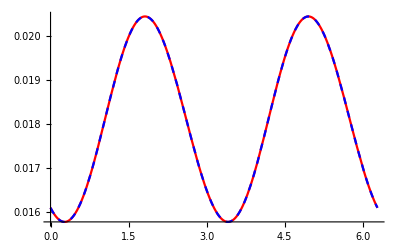

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

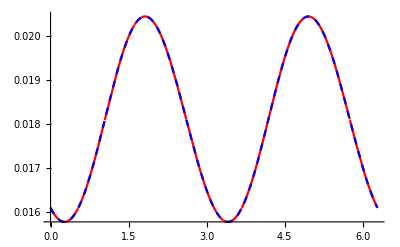
```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

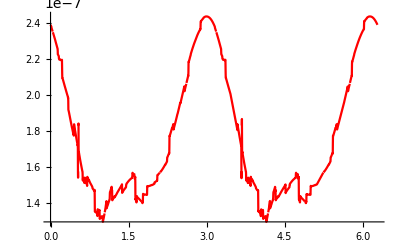

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

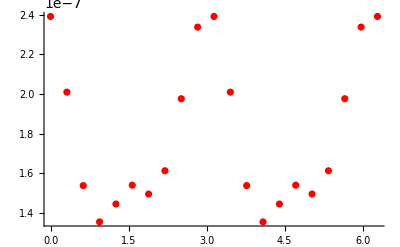

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b = 1

### r = 0.1

```mathematica
showdσHZ[bu,x1u,x3u,kT,False]
```

NIntegrate::inumr: The integrand Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] Sin[2 ϕ$143101] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}],{ϕ$143101,0,2 π}]/NIntegrate[dσHZ[x1u,x2u$143101,bu+x3u,bu+x4u$143101,{kT,ϕ$143101}],{ϕ$143101,0,2 π}],NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] Sin[2 ϕ$143101],{ϕ$143101,0,2 π}]/NIntegrate[dσHZ[x1u,x2u$143101,bu+x3u,bu+x4u$143101,{kT,ϕ$143101}],{ϕ$143101,0,2 π}]}

```mathematica
showdσHZ[2,bu,x1u,x3u,kT,False]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {4.52821}. NIntegrate obtained -7.82983×10^-8 and 1.56701×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {5.42406}. NIntegrate obtained 5.70936×10^-21 and 9.96811×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {4.0128}. NIntegrate obtained 1.41335×10^-7 and 2.29773×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.553992,4.0396×10^-14}

```mathematica
showdσHZ[4,bu,x1u,x3u,kT,False]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3516374 near {ϕ$3516374} = {5.26452}. NIntegrate obtained -6.47938×10^-13 and 3.88327×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3516374 near {ϕ$3516374} = {4.0128}. NIntegrate obtained 1.41335×10^-7 and 2.29773×10^-13 for the integral and error estimates.

{0.255988,-4.58442×10^-6}

```mathematica
v2kTr01={};
For[i=1,i≤120,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$146042 near {ϕ$146042} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$198005 near {ϕ$198005} = {5.08045}. NIntegrate obtained -4.84395×10^-16 and 2.90601×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$288347 near {ϕ$288347} = {4.20915}. NIntegrate obtained -4.10856×10^-18 and 3.96797×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
v2kTr01
```

{{0.25,{-0.0157187,4.45577×10^-15}},{0.5,{-0.062827,-9.20926×10^-12}},{0.75,{-0.139328,-2.00755×10^-13}},{1.,{-0.240227,1.77613×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.75,{-0.591091,7.7825×10^-10}},{2.,{-0.677349,-1.10209×10^-13}},{2.25,{-0.726966,2.70404×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.75,{-0.719943,-4.26028×10^-14}},{3.,{-0.684442,-2.18537×10^-10}},{3.25,{-0.643735,-1.25544×10^-6}},{3.5,{-0.605698,-1.79259×10^-14}},{3.75,{-0.574323,-4.14661×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{5.,{-0.528467,2.38943×10^-14}},{5.25,{-0.536388,2.11343×10^-8}},{5.5,{-0.548162,1.11488×10^-14}},{5.75,{-0.563122,5.39756×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.25,{-0.600009,4.35246×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.75,{-0.641511,4.96233×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.25,{-0.681019,1.36393×10^-14}},{7.5,{-0.697642,-1.31854×10^-14}},{7.75,{-0.710858,-2.09258×10^-14}},{8.,{-0.719767,-1.24401×10^-15}},{8.25,{-0.723653,-1.38475×10^-14}},{8.5,{-0.722076,2.28796×10^-14}},{8.75,{-0.714966,2.02798×10^-6}},{9.,{-0.702631,1.28915×10^-7}},{9.25,{-0.685778,7.09638×10^-15}},{9.5,{-0.665429,-8.58115×10^-8}},{9.75,{-0.642763,1.7996×10^-9}},{10.,{-0.619111,7.59579×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.5,{-0.573702,-4.43718×10^-7}},{10.75,{-0.553992,4.0396×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.25,{-0.523987,2.72869×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{13.,{-0.524609,2.11315×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.5,{-0.542427,-5.10646×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{14.,{-0.558401,-5.68867×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.25,{-0.560756,1.25152×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.75,{-0.543873,-9.58429×10^-15}},{16.,{-0.532927,-3.87923×10^-15}},{16.25,{-0.521115,-6.79951×10^-15}},{16.5,{-0.509113,8.01134×10^-14}},{16.75,{-0.497507,-3.77202×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.25,{-0.47777,3.74349×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{18.,{-0.461929,-4.03007×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.5,{-0.461883,-2.08973×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{19.,{-0.46897,-3.82806×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.75,{-0.4867,-1.72874×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.25,{-0.49782,-7.17622×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.75,{-0.504133,-4.93938×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.75,{-0.49478,8.20305×10^-15}},{22.,{-0.488089,2.61801×10^-8}},{22.25,{-0.480229,-5.37731×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.75,{-0.46269,-7.61967×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.25,{-0.445733,9.61877×10^-8}},{23.5,{-0.438406,-6.45213×10^-8}},{23.75,{-0.432338,-2.3747×10^-13}},{24.,{-0.427743,-9.23792×10^-8}},{24.25,{-0.424703,4.40993×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.75,{-0.423365,3.09228×10^-7}},{25.,{-0.42485,-3.94661×10^-14}},{25.25,{-0.427551,5.47303×10^-17}},{25.5,{-0.431117,-7.25639×10^-15}},{25.75,{-0.435291,-2.88181×10^-14}},{26.,{-0.439572,-1.21974×10^-14}},{26.25,{-0.44375,-1.4636×10^-8}},{26.5,{-0.447275,-1.24115×10^-6}},{26.75,{-0.449846,-2.78558×10^-15}},{27.,{-0.45121,4.63195×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.25,{-0.435217,1.81927×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{29.,{-0.411968,-2.64344×10^-7}},{29.25,{-0.40379,-6.46534×10^-9}},{29.5,{-0.396003,3.62264×10^-7}},{29.75,{-0.388929,2.53649×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

```mathematica
v2kTr01={};
For[i=1,i≤240,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr01
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192131759 near {ϕ$192131759} = {5.71858}. NIntegrate obtained 9.12678×10^-18 and 7.00796×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192194508 near {ϕ$192194508} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192246433 near {ϕ$192246433} = {1.90204}. NIntegrate obtained -3.23138×10^-18 and 3.01729×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{-0.00391806,9.24485×10^-15}},{0.25,{-0.0157187,4.45577×10^-15}},{0.375,{-0.0354044,-3.24943×10^-14}},{0.5,{-0.062827,-9.20926×10^-12}},{0.625,{-0.0976425,1.13234×10^-11}},{0.75,{-0.139328,-2.00755×10^-13}},{0.875,{-0.18716,3.65879×10^-14}},{1.,{-0.240227,1.77613×10^-12}},{1.125,{-0.297416,1.63936×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.375,{-0.418602,5.56247×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.625,{-0.537441,-4.3328×10^-12}},{1.75,{-0.591091,7.7825×10^-10}},{1.875,{-0.638266,-1.63048×10^-13}},{2.,{-0.677349,-1.10209×10^-13}},{2.125,{-0.707092,-2.29806×10^-14}},{2.25,{-0.726966,2.70404×10^-14}},{2.375,{-0.737136,6.27389×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.625,{-0.732143,6.6596×10^-14}},{2.75,{-0.719943,-4.26028×10^-14}},{2.875,{-0.703491,-5.24726×10^-15}},{3.,{-0.684442,-2.18537×10^-10}},{3.125,{-0.664112,2.06704×10^-7}},{3.25,{-0.643735,-1.25544×10^-6}},{3.375,{-0.624029,2.33796×10^-9}},{3.5,{-0.605698,-1.79259×10^-14}},{3.625,{-0.589021,3.152×10^-15}},{3.75,{-0.574323,-4.14661×10^-14}},{3.875,{-0.561591,3.64852×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.125,{-0.542226,1.09035×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.375,{-0.530442,4.75911×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.625,{-0.525386,3.59845×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{4.875,{-0.526151,2.7405×10^-14}},{5.,{-0.528467,2.38943×10^-14}},{5.125,{-0.531883,1.14919×10^-15}},{5.25,{-0.536388,2.11343×10^-8}},{5.375,{-0.54182,1.20107×10^-14}},{5.5,{-0.548162,1.11488×10^-14}},{5.625,{-0.555274,-8.20707×10^-15}},{5.75,{-0.563122,5.39756×10^-15}},{5.875,{-0.571586,7.41448×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.125,{-0.590118,1.36165×10^-14}},{6.25,{-0.600009,4.35246×10^-15}},{6.375,{-0.610183,6.64694×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.625,{-0.631035,-0.0000186778}},{6.75,{-0.641511,4.96233×10^-15}},{6.875,{-0.651861,2.55459×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.125,{-0.671738,-2.92902×10^-15}},{7.25,{-0.681019,1.36393×10^-14}},{7.375,{-0.689696,6.94386×10^-15}},{7.5,{-0.697642,-1.31854×10^-14}},{7.625,{-0.704735,5.44791×10^-15}},{7.75,{-0.710858,-2.09258×10^-14}},{7.875,{-0.715901,-9.91784×10^-15}},{8.,{-0.719767,-1.24401×10^-15}},{8.125,{-0.722373,1.05616×10^-14}},{8.25,{-0.723653,-1.38475×10^-14}},{8.375,{-0.723562,-1.03857×10^-6}},{8.5,{-0.722076,2.28796×10^-14}},{8.625,{-0.719204,-8.35843×10^-15}},{8.75,{-0.714966,2.02798×10^-6}},{8.875,{-0.709417,-5.23131×10^-15}},{9.,{-0.702631,1.28915×10^-7}},{9.125,{-0.694717,-2.14784×10^-14}},{9.25,{-0.685778,7.09638×10^-15}},{9.375,{-0.676018,5.70954×10^-10}},{9.5,{-0.665429,-8.58115×10^-8}},{9.625,{-0.65429,4.1604×10^-9}},{9.75,{-0.642763,1.7996×10^-9}},{9.875,{-0.630964,4.22605×10^-10}},{10.,{-0.619111,7.59579×10^-9}},{10.125,{-0.607292,-2.63884×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.375,{-0.584465,-1.55127×10^-8}},{10.5,{-0.573702,-4.43718×10^-7}},{10.625,{-0.56351,1.85527×10^-9}},{10.75,{-0.553992,4.0396×10^-14}},{10.875,{-0.545223,-1.78051×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.125,{-0.530179,4.19585×10^-14}},{11.25,{-0.523987,2.72869×10^-14}},{11.375,{-0.518713,2.44227×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.625,{-0.510956,-2.06649×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{11.875,{-0.506853,3.11422×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.125,{-0.506172,4.08252×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.375,{-0.50857,5.42349×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.625,{-0.513558,-2.71448×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{12.875,{-0.520556,-5.9532×10^-6}},{13.,{-0.524609,2.11315×10^-14}},{13.125,{-0.528908,-1.20543×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.375,{-0.537917,3.56506×10^-14}},{13.5,{-0.542427,-5.10646×10^-14}},{13.625,{-0.546816,-3.23183×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{13.875,{-0.554886,6.62078×10^-14}},{14.,{-0.558401,-5.68867×10^-9}},{14.125,{-0.561471,-2.89749×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.375,{-0.565932,-3.45317×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.625,{-0.567907,2.41045×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{14.875,{-0.567117,3.72258×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.125,{-0.563538,-7.51051×10^-14}},{15.25,{-0.560756,1.25152×10^-14}},{15.375,{-0.5573,3.55902×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.625,{-0.548818,-4.80804×10^-14}},{15.75,{-0.543873,-9.58429×10^-15}},{15.875,{-0.538548,9.39554×10^-8}},{16.,{-0.532927,-3.87923×10^-15}},{16.125,{-0.527067,4.65576×10^-14}},{16.25,{-0.521115,-6.79951×10^-15}},{16.375,{-0.515081,5.54892×10^-9}},{16.5,{-0.509113,8.01134×10^-14}},{16.625,{-0.503211,2.72188×10^-7}},{16.75,{-0.497507,-3.77202×10^-14}},{16.875,{-0.492054,-1.25119×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.125,{-0.482131,-7.41066×10^-15}},{17.25,{-0.47777,3.74349×10^-15}},{17.375,{-0.473844,5.9667×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.625,{-0.467491,4.3907×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{17.875,{-0.463243,-2.10496×10^-8}},{18.,{-0.461929,-4.03007×10^-14}},{18.125,{-0.461149,-6.54288×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.375,{-0.461134,-1.98077×10^-14}},{18.5,{-0.461883,-2.08973×10^-14}},{18.625,{-0.463071,6.68107×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{18.875,{-0.466657,-1.70866×10^-8}},{19.,{-0.46897,-3.82806×10^-14}},{19.125,{-0.471552,1.23226×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.375,{-0.47735,9.2783×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.625,{-0.483582,-5.14005×10^-14}},{19.75,{-0.4867,-1.72874×10^-14}},{19.875,{-0.489746,-1.59723×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.125,{-0.495363,7.63791×10^-15}},{20.25,{-0.49782,-7.17622×10^-14}},{20.375,{-0.499985,-1.57414×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.625,{-0.503164,-4.27794×10^-14}},{20.75,{-0.504133,-4.93938×10^-8}},{20.875,{-0.504649,4.76289×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.125,{-0.504224,-5.54497×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.375,{-0.50183,-6.0334×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.625,{-0.497555,6.92067×10^-14}},{21.75,{-0.49478,8.20305×10^-15}},{21.875,{-0.491599,3.77525×10^-14}},{22.,{-0.488089,2.61801×10^-8}},{22.125,{-0.484275,-5.54828×10^-14}},{22.25,{-0.480229,-5.37731×10^-14}},{22.375,{-0.475975,3.36491×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.625,{-0.467145,-1.30164×10^-13}},{22.75,{-0.46269,-7.61967×10^-8}},{22.875,{-0.458232,-8.47578×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.125,{-0.449626,1.29812×10^-13}},{23.25,{-0.445733,9.61877×10^-8}},{23.375,{-0.441914,-1.37089×10^-6}},{23.5,{-0.438406,-6.45213×10^-8}},{23.625,{-0.4352,4.34374×10^-15}},{23.75,{-0.432338,-2.3747×10^-13}},{23.875,{-0.429846,-2.68353×10^-6}},{24.,{-0.427743,-9.23792×10^-8}},{24.125,{-0.426012,-1.60375×10^-13}},{24.25,{-0.424703,4.40993×10^-14}},{24.375,{-0.423768,6.27334×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.625,{-0.423113,3.00584×10^-7}},{24.75,{-0.423365,3.09228×10^-7}},{24.875,{-0.423923,-2.36848×10^-14}},{25.,{-0.42485,-3.94661×10^-14}},{25.125,{-0.42606,-3.28257×10^-7}},{25.25,{-0.427551,5.47303×10^-17}},{25.375,{-0.429246,-1.18742×10^-14}},{25.5,{-0.431117,-7.25639×10^-15}},{25.625,{-0.433147,-1.20703×10^-7}},{25.75,{-0.435291,-2.88181×10^-14}},{25.875,{-0.437456,-2.9449×10^-8}},{26.,{-0.439572,-1.21974×10^-14}},{26.125,{-0.441723,4.65413×10^-8}},{26.25,{-0.44375,-1.4636×10^-8}},{26.375,{-0.445603,7.76898×10^-7}},{26.5,{-0.447275,-1.24115×10^-6}},{26.625,{-0.448714,-1.56567×10^-8}},{26.75,{-0.449846,-2.78558×10^-15}},{26.875,{-0.450702,1.62737×10^-14}},{27.,{-0.45121,4.63195×10^-7}},{27.125,{-0.451354,-9.7451×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.375,{-0.450448,-2.64888×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.625,{-0.447953,-8.43784×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{27.875,{-0.443904,-1.23919×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.125,{-0.438432,5.87047×10^-15}},{28.25,{-0.435217,1.81927×10^-14}},{28.375,{-0.431741,4.95195×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.625,{-0.424174,-4.26775×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{28.875,{-0.416064,-2.10964×10^-7}},{29.,{-0.411968,-2.64344×10^-7}},{29.125,{-0.407836,-7.9619×10^-16}},{29.25,{-0.40379,-6.46534×10^-9}},{29.375,{-0.399811,-3.37582×10^-7}},{29.5,{-0.396003,3.62264×10^-7}},{29.625,{-0.392349,4.68287×10^-8}},{29.75,{-0.388929,2.53649×10^-7}},{29.875,{-0.385746,2.70477×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

```mathematica
v2kTr01={{0.125,{-0.003918057710614559,9.244854885711647*^-15}},{0.25,{-0.015718719721257,4.455768613178577*^-15}},{0.375,{-0.035404393455990855,-3.24942552743455*^-14}},{0.5,{-0.06282700520498571,-9.209262174235287*^-12}},{0.625,{-0.09764251133096699,1.1323373487828947*^-11}},{0.75,{-0.13932777556625237,-2.0075541724325464*^-13}},{0.875,{-0.1871596950255955,3.6587891032648094*^-14}},{1.,{-0.2402268659614949,1.7761272106741705*^-12}},{1.125,{-0.29741608683685067,1.63936386445259*^-12}},{1.25,{-0.35738980707365536,-2.9331080873408746*^-14}},{1.375,{-0.41860210294753264,5.5624657311130876*^-14}},{1.5,{-0.4792613331839505,2.1483054629612167*^-11}},{1.625,{-0.5374405029017671,-4.33280410886713*^-12}},{1.75,{-0.5910905844362639,7.782502667849232*^-10}},{1.875,{-0.6382657283683378,-1.6304778766370707*^-13}},{2.,{-0.6773485071187965,-1.1020930550360381*^-13}},{2.125,{-0.7070922567638241,-2.2980585681298934*^-14}},{2.25,{-0.7269659742677628,2.704041641059906*^-14}},{2.375,{-0.7371361605396004,6.273889630496712*^-14}},{2.5,{-0.7384228508900981,1.0598538605139731*^-13}},{2.625,{-0.7321427588980837,6.659595237400903*^-14}},{2.75,{-0.7199432377360689,-4.260275997313958*^-14}},{2.875,{-0.7034905063569131,-5.247259673659533*^-15}},{3.,{-0.6844423879210192,-2.1853706117116236*^-10}},{3.125,{-0.6641124978889632,2.067040341464235*^-7}},{3.25,{-0.6437348216121175,-1.2554414576815327*^-6}},{3.375,{-0.6240287203305982,2.3379570679486058*^-9}},{3.5,{-0.6056977704518648,-1.7925891529668374*^-14}},{3.625,{-0.5890209403411332,3.1520035514624035*^-15}},{3.75,{-0.5743230810965477,-4.1466113956369136*^-14}},{3.875,{-0.5615908182140499,3.648522336489531*^-14}},{4.,{-0.5509450813004367,1.7927726800391485*^-14}},{4.125,{-0.5422263685405077,1.0903453666383883*^-14}},{4.25,{-0.535463471178256,1.70266968146611*^-14}},{4.375,{-0.5304417121950176,4.759113761210206*^-14}},{4.5,{-0.5271569742812412,3.128951738783436*^-14}},{4.625,{-0.5253862269155424,3.598453744249841*^-14}},{4.75,{-0.5251213439483727,-2.428438280829479*^-15}},{4.875,{-0.5261507000273551,2.740499076043137*^-14}},{5.,{-0.5284673400166482,2.3894269069901594*^-14}},{5.125,{-0.5318829019586997,1.149190308111416*^-15}},{5.25,{-0.5363884128225829,2.1134322259835257*^-8}},{5.375,{-0.5418199157681947,1.2010731556825687*^-14}},{5.5,{-0.5481620285702847,1.1148763365957442*^-14}},{5.625,{-0.5552737445041922,-8.207069955019638*^-15}},{5.75,{-0.5631222515577617,5.397564812856081*^-15}},{5.875,{-0.5715864634218168,7.414484970014047*^-15}},{6.,{-0.5806247305756812,4.77842247006239*^-15}},{6.125,{-0.5901175885917581,1.3616455397502957*^-14}},{6.25,{-0.6000091086421262,4.352458936126006*^-15}},{6.375,{-0.6101831594975383,6.646937432759431*^-15}},{6.5,{-0.6205652794316837,-3.958075861245624*^-15}},{6.625,{-0.6310351690619019,-0.000018677847951257842}},{6.75,{-0.641511244041416,4.962331055710025*^-15}},{6.875,{-0.6518606611667205,2.554591094168787*^-15}},{7.,{-0.6619780296717406,1.0836216739777441*^-14}},{7.125,{-0.6717382011865476,-2.9290169948253282*^-15}},{7.25,{-0.6810190635678771,1.3639273580277793*^-14}},{7.375,{-0.6896961869618619,6.943860915145641*^-15}},{7.5,{-0.6976424505607638,-1.318541182628416*^-14}},{7.625,{-0.7047345966199451,5.447913040411827*^-15}},{7.75,{-0.7108584400080679,-2.0925760370717457*^-14}},{7.875,{-0.7159012569390238,-9.91784094948124*^-15}},{8.,{-0.7197674742523701,-1.2440075599238084*^-15}},{8.125,{-0.7223729235444168,1.0561550325913656*^-14}},{8.25,{-0.7236530530050557,-1.3847475036530753*^-14}},{8.375,{-0.7235617043911938,-1.0385721845199884*^-6}},{8.5,{-0.7220755757408699,2.287960614425298*^-14}},{8.625,{-0.7192036223031588,-8.35843469193545*^-15}},{8.75,{-0.7149657237731009,2.027975084614235*^-6}},{8.875,{-0.7094169934332586,-5.231311626546625*^-15}},{9.,{-0.7026313798074314,1.2891481340484175*^-7}},{9.125,{-0.6947167039601682,-2.147836268823866*^-14}},{9.25,{-0.685777837770821,7.096383091306253*^-15}},{9.375,{-0.676018020597335,5.709536337482595*^-10}},{9.5,{-0.6654285735792814,-8.581145590162497*^-8}},{9.625,{-0.654289558294374,4.160395754737705*^-9}},{9.75,{-0.6427632459378138,1.7996043544820085*^-9}},{9.875,{-0.6309636673004227,4.226048165496085*^-10}},{10.,{-0.6191110639479821,7.595792922208492*^-9}},{10.125,{-0.6072917387608915,-2.638841929245373*^-9}},{10.25,{-0.5957188246440015,-3.1015597792991535*^-9}},{10.375,{-0.5844645343467849,-1.551269967745795*^-8}},{10.5,{-0.57370150503722,-4.4371818780436207*^-7}},{10.625,{-0.5635097362380815,1.8552656231098774*^-9}},{10.75,{-0.5539916214788152,4.0395969162598574*^-14}},{10.875,{-0.5452226924354484,-1.780511057889443*^-14}},{11.,{-0.5372698734812158,-4.744145593705214*^-9}},{11.125,{-0.5301790327086909,4.195848666449436*^-14}},{11.25,{-0.5239872611307822,2.728685607364563*^-14}},{11.375,{-0.5187128507420379,2.4422684108623936*^-14}},{11.5,{-0.5143725975494813,-3.496286680063301*^-14}},{11.625,{-0.510955748904712,-2.0664917798758742*^-14}},{11.75,{-0.5084597678727364,2.7881696845516474*^-14}},{11.875,{-0.5068530909992728,3.1142175367135745*^-14}},{12.,{-0.5061075684239557,-1.461442305709657*^-14}},{12.125,{-0.5061716891195183,4.0825170656166505*^-14}},{12.25,{-0.5070213530125814,2.1860598265125716*^-14}},{12.375,{-0.5085695649902339,5.423487024647039*^-14}},{12.5,{-0.510777510724057,-3.7298607318384654*^-14}},{12.625,{-0.5135580520205365,-2.7144829964143545*^-14}},{12.75,{-0.516843769387631,3.905077961491842*^-14}},{12.875,{-0.5205564772213358,-5.953200852970119*^-6}},{13.,{-0.5246091726286898,2.113148931274359*^-14}},{13.125,{-0.5289076310929574,-1.2054313735626946*^-14}},{13.25,{-0.5333844134675617,2.883326672743894*^-15}},{13.375,{-0.5379172659817382,3.56506201745071*^-14}},{13.5,{-0.5424269721690292,-5.1064580363419865*^-14}},{13.625,{-0.546815862479167,-3.2318346559616534*^-14}},{13.75,{-0.551003726867789,2.1615203883493048*^-6}},{13.875,{-0.5548861803313295,6.620780524955221*^-14}},{14.,{-0.5584008919648269,-5.688665305842023*^-9}},{14.125,{-0.5614709362637526,-2.897494281422422*^-9}},{14.25,{-0.5639898471470772,-4.1928217124719556*^-14}},{14.375,{-0.5659324345221263,-3.4531692542762257*^-14}},{14.5,{-0.5672586242649905,-4.807176917575697*^-14}},{14.625,{-0.5679067183134074,2.4104502828648115*^-14}},{14.75,{-0.5678747986966025,4.710647930983182*^-14}},{14.875,{-0.5671169769243197,3.72258226325579*^-14}},{15.,{-0.5656816070173624,8.06852755841809*^-15}},{15.125,{-0.5635384254091744,-7.510508136295701*^-14}},{15.25,{-0.56075552551836,1.25152175074836*^-14}},{15.375,{-0.5573004513694695,3.5590212147582575*^-14}},{15.5,{-0.5533341837568391,9.577606751690335*^-10}},{15.625,{-0.5488184443536331,-4.8080410027081485*^-14}},{15.75,{-0.5438728526359264,-9.584287837352239*^-15}},{15.875,{-0.5385484248118637,9.3955412023375*^-8}},{16.,{-0.5329268665170057,-3.8792326671220296*^-15}},{16.125,{-0.527067341734732,4.655757932398242*^-14}},{16.25,{-0.5211152931915697,-6.7995068199288484*^-15}},{16.375,{-0.5150812721601088,5.548916646547927*^-9}},{16.5,{-0.5091125901884977,8.011336983399773*^-14}},{16.625,{-0.503210597506499,2.7218779042229064*^-7}},{16.75,{-0.49750694351250224,-3.772022823975667*^-14}},{16.875,{-0.4920537949899836,-1.2511884263301538*^-14}},{17.,{-0.48691881104524515,-5.345949023786466*^-14}},{17.125,{-0.4821307158749294,-7.410663561568436*^-15}},{17.25,{-0.47777045845568183,3.7434932908790614*^-15}},{17.375,{-0.47384415636903865,5.966703863615523*^-15}},{17.5,{-0.4704211495107554,7.532302330341834*^-14}},{17.625,{-0.46749090679274174,4.390700693813543*^-14}},{17.75,{-0.4651098856213215,-4.735876892443972*^-15}},{17.875,{-0.46324289313407163,-2.104956549555236*^-8}},{18.,{-0.4619286731818374,-4.030065275947804*^-14}},{18.125,{-0.461149077605719,-6.542881813006678*^-14}},{18.25,{-0.460895788762363,2.940479971703702*^-6}},{18.375,{-0.46113375363503656,-1.980772529508429*^-14}},{18.5,{-0.461883473081167,-2.0897297555967427*^-14}},{18.625,{-0.46307099222403986,6.681066146310082*^-14}},{18.75,{-0.46468060214693285,-1.177628293229202*^-14}},{18.875,{-0.4666571776539901,-1.7086602708282606*^-8}},{19.,{-0.46896956430538544,-3.828063149989548*^-14}},{19.125,{-0.4715519322773859,1.2322568083549429*^-14}},{19.25,{-0.4743706366449681,1.8680041343858585*^-14}},{19.375,{-0.4773503356144509,9.278299313068467*^-14}},{19.5,{-0.480430334113364,1.0318391124324963*^-13}},{19.625,{-0.4835823912600917,-5.14004639915888*^-14}},{19.75,{-0.4866998422630719,-1.7287423727555124*^-14}},{19.875,{-0.4897457666307268,-1.597230991496991*^-14}},{20.,{-0.4926391948866737,-3.25636684229374*^-6}},{20.125,{-0.4953630392999924,7.63791365314107*^-15}},{20.25,{-0.4978198385421389,-7.17621977032122*^-14}},{20.375,{-0.4999851266323586,-1.5741426666256957*^-14}},{20.5,{-0.5017369547339656,9.254957801709921*^-15}},{20.625,{-0.5031636579503245,-4.2779378693736176*^-14}},{20.75,{-0.5041334259129382,-4.9393755943928894*^-8}},{20.875,{-0.5046489107715457,4.76288951391161*^-8}},{21.,{-0.5046801237408688,5.344459368659944*^-8}},{21.125,{-0.504223877709701,-5.5449739133984515*^-8}},{21.25,{-0.5032732619523007,6.489640882211827*^-14}},{21.375,{-0.5018302417174715,-6.033401053662525*^-14}},{21.5,{-0.49992571609102104,6.127152660289473*^-8}},{21.625,{-0.49755516133334904,6.920669434659163*^-14}},{21.75,{-0.4947798164341914,8.203047498184611*^-15}},{21.875,{-0.49159876889154186,3.7752479276997184*^-14}},{22.,{-0.4880890150013355,2.6180097567770878*^-8}},{22.125,{-0.4842748163077433,-5.5482811489787554*^-14}},{22.25,{-0.4802293154570574,-5.377307437107822*^-14}},{22.375,{-0.4759754602071142,3.364912282960911*^-14}},{22.5,{-0.471635866831603,-2.3764486157273692*^-8}},{22.625,{-0.4671447714425382,-1.3016389315369388*^-13}},{22.75,{-0.46268986296936804,-7.619666953358566*^-8}},{22.875,{-0.45823245579980426,-8.475776061132287*^-8}},{23.,{-0.45388331389909664,-4.358226719250919*^-14}},{23.125,{-0.4496261773431517,1.2981206420934466*^-13}},{23.25,{-0.4457326712051796,9.618772204798758*^-8}},{23.375,{-0.44191434974351523,-1.3708939314195487*^-6}},{23.5,{-0.4384057757477033,-6.452133754270889*^-8}},{23.625,{-0.4352000848031097,4.343737142225139*^-15}},{23.75,{-0.4323384936006302,-2.374703016560287*^-13}},{23.875,{-0.4298464001530676,-2.6835303414091216*^-6}},{24.,{-0.42774329253115484,-9.237924090252065*^-8}},{24.125,{-0.4260122730013701,-1.6037490877630148*^-13}},{24.25,{-0.4247031567019669,4.409930619066391*^-14}},{24.375,{-0.42376795667412026,6.273343426917469*^-14}},{24.5,{-0.4232523021784899,-1.1754861454399368*^-14}},{24.625,{-0.42311307956741384,3.0058374124292336*^-7}},{24.75,{-0.4233649059889497,3.092283985634873*^-7}},{24.875,{-0.42392298901895437,-2.368480464842721*^-14}},{25.,{-0.42485047255910835,-3.946606557341267*^-14}},{25.125,{-0.42606027925299195,-3.282572556989622*^-7}},{25.25,{-0.42755088604521085,5.4730319659071236*^-17}},{25.375,{-0.4292463383192781,-1.1874230210186027*^-14}},{25.5,{-0.4311171000966129,-7.256387564780687*^-15}},{25.625,{-0.43314686190293206,-1.2070281234177507*^-7}},{25.75,{-0.43529145102834615,-2.881805837704058*^-14}},{25.875,{-0.4374557756665144,-2.9449024212099173*^-8}},{26.,{-0.43957192800694617,-1.2197409264483674*^-14}},{26.125,{-0.441722961502819,4.654125022016889*^-8}},{26.25,{-0.443750308925389,-1.4635979953332415*^-8}},{26.375,{-0.44560321163111033,7.768982996323666*^-7}},{26.5,{-0.44727461468616014,-1.2411452655714186*^-6}},{26.625,{-0.44871350918640085,-1.5656745865351604*^-8}},{26.75,{-0.44984616406922656,-2.7855840196869317*^-15}},{26.875,{-0.4507019432825056,1.6273714362356918*^-14}},{27.,{-0.45121017341818476,4.631950585133083*^-7}},{27.125,{-0.4513544106332651,-9.745103498577046*^-7}},{27.25,{-0.45111319996299515,2.4201012930772588*^-14}},{27.375,{-0.4504476558170241,-2.6488805190751227*^-14}},{27.5,{-0.44942414196121505,9.530213205262386*^-15}},{27.625,{-0.4479534600519532,-8.437836593057415*^-15}},{27.75,{-0.446122732979754,2.4679867204052903*^-14}},{27.875,{-0.4439039480821522,-1.239187635463128*^-14}},{28.,{-0.441333010915874,-2.275395158346231*^-6}},{28.125,{-0.4384324819950191,5.870473379266322*^-15}},{28.25,{-0.4352168639917436,1.819273635604562*^-14}},{28.375,{-0.43174072945042513,4.9519451179217836*^-14}},{28.5,{-0.42804991239419665,5.970586863076394*^-14}},{28.625,{-0.4241736359202971,-4.2677503346019027*^-14}},{28.75,{-0.4202032069696325,1.0879005736680512*^-14}},{28.875,{-0.41606411033910085,-2.1096354416855767*^-7}},{29.,{-0.4119681248300768,-2.643443418682811*^-7}},{29.125,{-0.40783575377292375,-7.961902697241522*^-16}},{29.25,{-0.40378988368510366,-6.465343161779006*^-9}},{29.375,{-0.3998109555466155,-3.3758241775275253*^-7}},{29.5,{-0.3960027985608335,3.622637540194912*^-7}},{29.625,{-0.39234925257912306,4.682866576419484*^-8}},{29.75,{-0.3889291027409299,2.5364903611170395*^-7}},{29.875,{-0.38574645668502355,2.704772699814783*^-7}},{30.,{-0.3828198488896162,-2.6158514875207895*^-14}}};
```

```mathematica
v4kTr01={};
For[i=1,i≤240,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr01,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr01
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3618577 near {ϕ$3618577} = {5.71858}. NIntegrate obtained 3.48462×10^-9 and 1.24428×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3618577 near {ϕ$3618577} = {5.71858}. NIntegrate obtained 1.67289×10^-13 and 2.56095×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3785470 near {ϕ$3785470} = {4.08643}. NIntegrate obtained 1.35159×10^-8 and 1.52543×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{3.5297×10^-6,1.69453×10^-10}},{0.25,{0.0000571857,-5.34902×10^-10}},{0.375,{0.000294395,-1.30601×10^-9}},{0.5,{0.000945763,7.77634×10^-9}},{0.625,{0.00234095,1.28529×10^-9}},{0.75,{0.0049063,-7.44241×10^-10}},{0.875,{0.00914927,1.43357×10^-9}},{1.,{0.0156382,1.9551×10^-9}},{1.125,{0.0249617,-1.16834×10^-9}},{1.25,{0.0376813,-7.92907×10^-9}},{1.375,{0.0542556,1.82624×10^-8}},{1.5,{0.0749647,2.49224×10^-9}},{1.625,{0.0998211,-3.34515×10^-9}},{1.75,{0.128488,-5.27857×10^-8}},{1.875,{0.160254,-2.36974×10^-7}},{2.,{0.194023,-6.06946×10^-8}},{2.125,{0.228419,-1.26761×10^-7}},{2.25,{0.261985,-1.30279×10^-8}},{2.375,{0.29324,-4.00362×10^-9}},{2.5,{0.320964,2.30572×10^-8}},{2.625,{0.34432,-1.6862×10^-8}},{2.75,{0.362823,-5.19414×10^-9}},{2.875,{0.37643,1.64074×10^-8}},{3.,{0.385356,-9.48803×10^-7}},{3.125,{0.390093,-4.69569×10^-6}},{3.25,{0.391192,-4.154×10^-6}},{3.375,{0.389315,4.45814×10^-8}},{3.5,{0.385059,2.32376×10^-8}},{3.625,{0.379006,-4.14458×10^-7}},{3.75,{0.371647,-5.97487×10^-7}},{3.875,{0.363403,2.24326×10^-6}},{4.,{0.35466,4.37033×10^-7}},{4.125,{0.345679,1.00228×10^-7}},{4.25,{0.336703,9.72904×10^-8}},{4.375,{0.327919,-1.31129×10^-8}},{4.5,{0.319486,-2.52443×10^-6}},{4.625,{0.311474,8.44867×10^-8}},{4.75,{0.304018,5.95081×10^-8}},{4.875,{0.297168,-1.79842×10^-7}},{5.,{0.290982,2.32001×10^-7}},{5.125,{0.285478,2.8268×10^-6}},{5.25,{0.280733,1.26649×10^-7}},{5.375,{0.27672,2.66961×10^-7}},{5.5,{0.273476,6.82615×10^-8}},{5.625,{0.270999,7.3285×10^-7}},{5.75,{0.269301,2.02908×10^-7}},{5.875,{0.268372,5.14749×10^-9}},{6.,{0.268218,5.83631×10^-7}},{6.125,{0.26881,-1.82903×10^-7}},{6.25,{0.270152,2.12391×10^-7}},{6.375,{0.272204,-1.35339×10^-8}},{6.5,{0.274955,-1.79912×10^-7}},{6.625,{0.278335,5.92001×10^-6}},{6.75,{0.282376,4.12469×10^-7}},{6.875,{0.286954,-1.21038×10^-7}},{7.,{0.292034,1.42681×10^-7}},{7.125,{0.297566,1.40175×10^-7}},{7.25,{0.303448,-2.55463×10^-6}},{7.375,{0.309609,8.1248×10^-8}},{7.5,{0.315949,-4.40041×10^-8}},{7.625,{0.322362,-1.83849×10^-8}},{7.75,{0.328743,4.92083×10^-8}},{7.875,{0.334969,3.82155×10^-8}},{8.,{0.340923,2.95913×10^-7}},{8.125,{0.346483,-4.07468×10^-7}},{8.25,{0.351525,-1.74602×10^-7}},{8.375,{0.355933,4.96545×10^-7}},{8.5,{0.359584,1.66278×10^-6}},{8.625,{0.362394,-9.43274×10^-7}},{8.75,{0.364259,-8.89703×10^-6}},{8.875,{0.365106,-5.23067×10^-6}},{9.,{0.364878,-8.98368×10^-7}},{9.125,{0.363505,-0.0000211529}},{9.25,{0.361037,-1.52929×10^-7}},{9.375,{0.35737,-3.26803×10^-6}},{9.5,{0.352627,7.3278×10^-6}},{9.625,{0.346768,3.89699×10^-6}},{9.75,{0.339861,-0.0000297583}},{9.875,{0.33194,5.93842×10^-7}},{10.,{0.323124,0.0000206669}},{10.125,{0.313455,-3.813×10^-6}},{10.25,{0.30307,1.71555×10^-6}},{10.375,{0.292022,-5.10672×10^-7}},{10.5,{0.280427,-1.56864×10^-7}},{10.625,{0.268381,6.02915×10^-7}},{10.75,{0.255988,-4.58442×10^-6}},{10.875,{0.243347,1.31971×10^-6}},{11.,{0.230506,-1.308×10^-6}},{11.125,{0.217616,4.14332×10^-6}},{11.25,{0.20472,4.41699×10^-7}},{11.375,{0.191921,-8.02642×10^-7}},{11.5,{0.17928,-4.44014×10^-7}},{11.625,{0.166873,-0.0000121088}},{11.75,{0.154776,-4.0614×10^-7}},{11.875,{0.143033,3.56433×10^-6}},{12.,{0.131707,6.89836×10^-6}},{12.125,{0.120841,-3.20828×10^-6}},{12.25,{0.110494,3.18887×10^-6}},{12.375,{0.100693,2.88469×10^-6}},{12.5,{0.0914997,-0.0000164344}},{12.625,{0.0828626,0.0000145044}},{12.75,{0.0749936,7.54661×10^-7}},{12.875,{0.0677644,-6.41489×10^-6}},{13.,{0.0612013,-1.84782×10^-6}},{13.125,{0.0553862,0.000101978}},{13.25,{0.0503204,-1.01596×10^-6}},{13.375,{0.0459627,2.06523×10^-6}},{13.5,{0.0423176,-2.17215×10^-6}},{13.625,{0.0393961,2.00969×10^-6}},{13.75,{0.0371762,4.28781×10^-6}},{13.875,{0.0356308,0.000020342}},{14.,{0.0347426,2.50653×10^-6}},{14.125,{0.0344399,-2.28254×10^-7}},{14.25,{0.0347451,-1.50938×10^-6}},{14.375,{0.0355338,2.18188×10^-6}},{14.5,{0.0368014,1.92445×10^-6}},{14.625,{0.0384558,-8.68593×10^-7}},{14.75,{0.0404517,-0.0000116105}},{14.875,{0.0426913,-1.21124×10^-6}},{15.,{0.0451502,1.4684×10^-7}},{15.125,{0.0477158,-1.956×10^-6}},{15.25,{0.0503301,7.89724×10^-7}},{15.375,{0.0528899,1.64273×10^-6}},{15.5,{0.0554233,-0.0000305596}},{15.625,{0.0577679,5.23555×10^-6}},{15.75,{0.0598912,-0.0000255544}},{15.875,{0.0618021,2.62105×10^-6}},{16.,{0.0633768,-0.000012681}},{16.125,{0.0645835,5.15215×10^-6}},{16.25,{0.0654298,2.84188×10^-6}},{16.375,{0.0658535,4.16213×10^-7}},{16.5,{0.0658789,1.29093×10^-6}},{16.625,{0.065461,3.94003×10^-6}},{16.75,{0.0645632,1.71633×10^-6}},{16.875,{0.0633025,-1.65834×10^-6}},{17.,{0.0615877,2.24594×10^-6}},{17.125,{0.0594634,-1.57749×10^-7}},{17.25,{0.0569498,-2.90069×10^-6}},{17.375,{0.0540616,1.9943×10^-7}},{17.5,{0.0508384,3.99054×10^-7}},{17.625,{0.0473126,-1.91527×10^-6}},{17.75,{0.0435107,-0.0000165802}},{17.875,{0.0394688,0.0000240941}},{18.,{0.0352165,-6.13396×10^-6}},{18.125,{0.0308359,0.0000427578}},{18.25,{0.0263104,5.67961×10^-7}},{18.375,{0.0217194,0.0000118516}},{18.5,{0.0171033,-4.62735×10^-6}},{18.625,{0.0124945,3.29559×10^-6}},{18.75,{0.00793259,1.39009×10^-6}},{18.875,{0.00345972,1.6121×10^-8}},{19.,{-0.000868284,-6.73179×10^-7}},{19.125,{-0.00503479,-4.75854×10^-8}},{19.25,{-0.0089781,-1.29483×10^-7}},{19.375,{-0.0127021,4.49295×10^-7}},{19.5,{-0.016136,5.15229×10^-6}},{19.625,{-0.0192556,2.29941×10^-7}},{19.75,{-0.022071,-1.29517×10^-6}},{19.875,{-0.0245321,-8.03315×10^-7}},{20.,{-0.0266234,7.23675×10^-6}},{20.125,{-0.0283325,1.24743×10^-6}},{20.25,{-0.0296702,-3.39329×10^-7}},{20.375,{-0.0305961,1.08248×10^-6}},{20.5,{-0.0312249,-6.57797×10^-7}},{20.625,{-0.0313982,-1.45273×10^-6}},{20.75,{-0.0312512,-0.0000162844}},{20.875,{-0.0307734,0.0000380855}},{21.,{-0.0299908,-0.0000171292}},{21.125,{-0.0289429,1.96033×10^-6}},{21.25,{-0.0276454,-5.21569×10^-6}},{21.375,{-0.0261518,9.95972×10^-6}},{21.5,{-0.0244833,0.0000300659}},{21.625,{-0.0227246,-0.0000426486}},{21.75,{-0.0208619,-9.46952×10^-6}},{21.875,{-0.0189876,0.0000158148}},{22.,{-0.0171248,7.96744×10^-7}},{22.125,{-0.0153193,4.25309×10^-7}},{22.25,{-0.0136179,7.26307×10^-6}},{22.375,{-0.0120586,-6.39231×10^-14}},{22.5,{-0.0106429,-1.7509×10^-7}},{22.625,{-0.00945772,-1.11936×10^-6}},{22.75,{-0.00851841,-5.81878×10^-8}},{22.875,{-0.00782957,-5.97171×10^-8}},{23.,{-0.00741986,3.95651×10^-14}},{23.125,{-0.00742567,3.77385×10^-6}},{23.25,{-0.00750246,-1.00238×10^-7}},{23.375,{-0.00802411,1.0317×10^-7}},{23.5,{-0.00888044,-1.00182×10^-7}},{23.625,{-0.0100185,-1.67735×10^-14}},{23.75,{-0.0115045,3.71669×10^-13}},{23.875,{-0.0132344,-4.35263×10^-6}},{24.,{-0.0152596,-1.47449×10^-7}},{24.125,{-0.0175411,1.53483×10^-7}},{24.25,{-0.0200814,1.5358×10^-7}},{24.375,{-0.0228448,1.60809×10^-7}},{24.5,{-0.0258069,-2.30486×10^-14}},{24.625,{-0.0289108,1.65743×10^-7}},{24.75,{-0.0321707,-7.9755×10^-7}},{24.875,{-0.0355361,-5.04094×10^-8}},{25.,{-0.0389792,-1.64552×10^-14}},{25.125,{-0.0424517,3.41426×10^-7}},{25.25,{-0.0459324,5.59465×10^-15}},{25.375,{-0.049402,2.07892×10^-14}},{25.5,{-0.052802,1.46725×10^-14}},{25.625,{-0.0560772,-1.95571×10^-14}},{25.75,{-0.0592095,4.97469×10^-14}},{25.875,{-0.0622478,3.93823×10^-8}},{26.,{-0.0651031,6.3295×10^-8}},{26.125,{-0.0676568,-5.13795×10^-8}},{26.25,{-0.0700418,2.12889×10^-9}},{26.375,{-0.0721377,-7.9186×10^-7}},{26.5,{-0.0739724,-7.0932×10^-8}},{26.625,{-0.0755192,-1.47334×10^-8}},{26.75,{-0.0767852,6.63642×10^-8}},{26.875,{-0.0777158,-7.0451×10^-8}},{27.,{-0.0783737,7.48096×10^-8}},{27.125,{-0.0787167,8.12191×10^-7}},{27.25,{-0.0787987,-8.96431×10^-8}},{27.375,{-0.0786257,3.8433×10^-14}},{27.5,{-0.0781563,-5.49111×10^-7}},{27.625,{-0.077509,-3.46833×10^-6}},{27.75,{-0.076657,-3.37175×10^-14}},{27.875,{-0.0756187,8.07865×10^-8}},{28.,{-0.0744614,4.03567×10^-6}},{28.125,{-0.0731546,-4.03335×10^-6}},{28.25,{-0.071874,-4.26477×10^-14}},{28.375,{-0.0705288,8.49629×10^-8}},{28.5,{-0.0691899,1.71488×10^-6}},{28.625,{-0.0678998,1.07644×10^-15}},{28.75,{-0.066618,3.11708×10^-14}},{28.875,{-0.0656087,2.59463×10^-7}},{29.,{-0.0646474,-1.81366×10^-7}},{29.125,{-0.0638895,-2.0805×10^-7}},{29.25,{-0.0633022,2.36137×10^-7}},{29.375,{-0.0629638,-2.65176×10^-7}},{29.5,{-0.0628476,2.94897×10^-7}},{29.625,{-0.0630162,2.90621×10^-7}},{29.75,{-0.0634242,3.55116×10^-7}},{29.875,{-0.0641262,3.84891×10^-7}},{30.,{-0.0651219,-4.13947×10^-7}}}

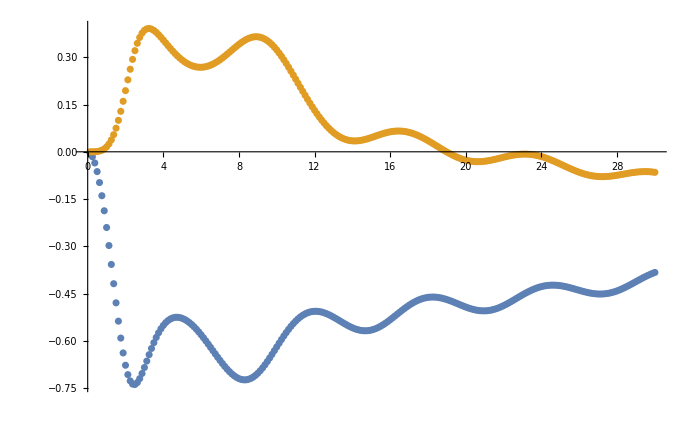

```mathematica
ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v4kTr01[[All,1]],Re[v4kTr01[[All,2,1]]]}]}]
```

### r = 0.25

```mathematica
v2kTr025={};
For[i=1,i≤120,i++,
x1u=1/8{Cos[π/2],Sin[π/2]};
x3u=1/8{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr025,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110680692 near {ϕ$110680692} = {2.3561}. NIntegrate obtained -2.11419×10^-18 and 5.0358×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110754266 near {ϕ$110754266} = {5.22771}. NIntegrate obtained 2.25448×10^-16 and 1.80831×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110874374 near {ϕ$110874374} = {2.08612}. NIntegrate obtained 1.82115×10^-16 and 1.83901×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr025
```

{{0.25,{-0.0157221,-2.41379×10^-16}},{0.5,{-0.0628756,1.16033×10^-13}},{0.75,{-0.139514,2.41869×10^-13}},{1.,{-0.240682,-9.41755×10^-14}},{1.25,{-0.358253,-7.55837×10^-16}},{1.5,{-0.480566,1.1285×10^-16}},{1.75,{-0.592539,7.92261×10^-10}},{2.,{-0.678149,-6.70196×10^-15}},{2.25,{-0.726055,4.35925×10^-15}},{2.5,{-0.735045,-1.94286×10^-15}},{2.75,{-0.714107,2.50598×10^-15}},{3.,{-0.676825,-7.80316×10^-10}},{3.25,{-0.63525,2.10671×10^-7}},{3.5,{-0.597127,1.51335×10^-15}},{3.75,{-0.566174,1.03888×10^-10}},{4.,{-0.543477,1.1877×10^-15}},{4.25,{-0.528769,3.27477×10^-8}},{4.5,{-0.521233,6.1827×10^-16}},{4.75,{-0.519932,-9.05992×10^-8}},{5.,{-0.523973,3.47998×10^-16}},{5.25,{-0.532572,6.42106×10^-11}},{5.5,{-0.545035,-1.38116×10^-10}},{5.75,{-0.560729,-2.23483×10^-15}},{6.,{-0.579039,3.38877×10^-15}},{6.25,{-0.599325,-3.26078×10^-11}},{6.5,{-0.620877,-2.05654×10^-15}},{6.75,{-0.642886,1.53868×10^-15}},{7.,{-0.664418,1.77479×10^-15}},{7.25,{-0.684415,1.00659×10^-15}},{7.5,{-0.701722,-6.23953×10^-16}},{7.75,{-0.715139,2.25239×10^-15}},{8.,{-0.723523,3.17998×10^-15}},{8.25,{-0.725913,2.10652×10^-15}},{8.5,{-0.721664,1.6207×10^-15}},{8.75,{-0.710577,-5.01832×10^-15}},{9.,{-0.692965,-7.57584×10^-11}},{9.25,{-0.669651,-2.82211×10^-10}},{9.5,{-0.641937,-1.9695×10^-9}},{9.75,{-0.611325,1.14119×10^-9}},{10.,{-0.579539,-5.10811×10^-10}},{10.25,{-0.548201,-1.45764×10^-10}},{10.5,{-0.518731,-1.98419×10^-9}},{10.75,{-0.492295,3.74871×10^-8}},{11.,{-0.469759,6.52556×10^-6}},{11.25,{-0.45166,-2.02602×10^-9}},{11.5,{-0.438295,-8.69866×10^-7}},{11.75,{-0.429698,1.20137×10^-15}},{12.,{-0.425696,8.1348×10^-16}},{12.25,{-0.42594,-1.11964×10^-14}},{12.5,{-0.429913,-1.0847×10^-7}},{12.75,{-0.436951,1.09338×10^-14}},{13.,{-0.446214,-2.71472×10^-15}},{13.25,{-0.456739,1.43915×10^-15}},{13.5,{-0.467414,-9.94575×10^-15}},{13.75,{-0.477044,5.02243×10^-7}},{14.,{-0.484355,-4.10757×10^-7}},{14.25,{-0.48817,-3.62165×10^-10}},{14.5,{-0.487432,6.46763×10^-15}},{14.75,{-0.481372,-7.86929×10^-15}},{15.,{-0.469619,-1.39306×10^-15}},{15.25,{-0.452244,-6.25834×10^-10}},{15.5,{-0.429791,-1.1628×10^-14}},{15.75,{-0.403218,-1.07527×10^-14}},{16.,{-0.373778,-5.27398×10^-7}},{16.25,{-0.342879,-2.90102×10^-7}},{16.5,{-0.31193,-8.95848×10^-7}},{16.75,{-0.282237,-1.65425×10^-9}},{17.,{-0.254889,7.14438×10^-9}},{17.25,{-0.230748,7.93413×10^-8}},{17.5,{-0.210411,-1.74149×10^-8}},{17.75,{-0.194243,2.43155×10^-8}},{18.,{-0.182385,4.86987×10^-9}},{18.25,{-0.174785,4.519×10^-7}},{18.5,{-0.171196,-2.55907×10^-9}},{18.75,{-0.171198,7.27569×10^-15}},{19.,{-0.174184,-5.75667×10^-15}},{19.25,{-0.179345,-9.05611×10^-15}},{19.5,{-0.185657,1.89456×10^-6}},{19.75,{-0.191878,8.16411×10^-9}},{20.,{-0.196565,-2.33297×10^-9}},{20.25,{-0.198138,1.93264×10^-9}},{20.5,{-0.195009,-4.48211×10^-9}},{20.75,{-0.185756,1.23731×10^-8}},{21.,{-0.16933,3.92504×10^-10}},{21.25,{-0.145285,-1.95049×10^-9}},{21.5,{-0.113923,-9.26632×10^-16}},{21.75,{-0.0762806,-1.33097×10^-9}},{22.,{-0.0340279,-1.32369×10^-8}},{22.25,{0.0107713,2.13528×10^-14}},{22.5,{0.0559492,-7.3274×10^-8}},{22.75,{0.0996921,-3.06299×10^-8}},{23.,{0.140306,7.72214×10^-8}},{23.25,{0.176586,-4.51354×10^-8}},{23.5,{0.207716,1.45684×10^-7}},{23.75,{0.23341,-1.44263×10^-7}},{24.,{0.253535,4.66774×10^-8}},{24.25,{0.26813,6.59985×10^-9}},{24.5,{0.277439,-1.79015×10^-7}},{24.75,{0.281807,2.19601×10^-8}},{25.,{0.281729,6.15917×10^-8}},{25.25,{0.277797,-9.25834×10^-16}},{25.5,{0.270708,-1.84115×10^-7}},{25.75,{0.261542,-4.15435×10^-8}},{26.,{0.251566,-3.59209×10^-7}},{26.25,{0.242349,9.22774×10^-8}},{26.5,{0.235681,9.40175×10^-9}},{26.75,{0.233438,-9.03462×10^-8}},{27.,{0.237091,-1.28148×10^-7}},{27.25,{0.24743,-8.29506×10^-8}},{27.5,{0.264215,6.20238×10^-8}},{27.75,{0.28608,-7.58276×10^-7}},{28.,{0.310809,3.69901×10^-8}},{28.25,{0.335914,4.30307×10^-8}},{28.5,{0.359061,-1.41654×10^-8}},{28.75,{0.378408,-1.55423×10^-7}},{29.,{0.392657,-1.4651×10^-7}},{29.25,{0.401143,-7.95764×10^-8}},{29.5,{0.403514,-3.01587×10^-7}},{29.75,{0.39963,3.18068×10^-7}},{30.,{0.389552,-2.93246×10^-7}}}

### r = 0.5

```mathematica
v2kTr05={};
For[i=1,i≤120,i++,
x1u=1/4{Cos[π/2],Sin[π/2]};
x3u=1/4{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119294760 near {ϕ$119294760} = {2.47882}. NIntegrate obtained -4.78133×10^-17 and 1.44362×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119366529 near {ϕ$119366529} = {5.35043}. NIntegrate obtained -1.52×10^-15 and 1.84099×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119452361 near {ϕ$119452361} = {2.08612}. NIntegrate obtained 3.65414×10^-15 and 1.00431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr05
```

{{0.25,{-0.0157083,-4.05279×10^-16}},{0.5,{-0.0629432,-5.87232×10^-14}},{0.75,{-0.139938,3.69346×10^-13}},{1.,{-0.241898,-9.80784×10^-14}},{1.25,{-0.360771,-5.61855×10^-15}},{1.5,{-0.484544,2.26672×10^-12}},{1.75,{-0.596931,-9.49207×10^-9}},{2.,{-0.680079,3.49782×10^-16}},{2.25,{-0.721722,6.38164×10^-14}},{2.5,{-0.722091,2.49838×10^-16}},{2.75,{-0.693155,-2.94402×10^-11}},{3.,{-0.650732,-1.1387×10^-16}},{3.25,{-0.6073,-6.59918×10^-8}},{3.5,{-0.569821,7.27002×10^-9}},{3.75,{-0.540937,-2.13394×10^-9}},{4.,{-0.520875,-4.96253×10^-11}},{4.25,{-0.508864,2.21709×10^-8}},{4.5,{-0.503829,2.57298×10^-16}},{4.75,{-0.504775,-2.18389×10^-16}},{5.,{-0.510865,-3.66857×10^-17}},{5.25,{-0.521426,8.46509×10^-9}},{5.5,{-0.535909,1.07528×10^-17}},{5.75,{-0.553836,-8.01161×10^-16}},{6.,{-0.574735,-5.15664×10^-11}},{6.25,{-0.59807,4.81692×10^-11}},{6.5,{-0.623166,-5.52602×10^-11}},{6.75,{-0.649125,1.71295×10^-12}},{7.,{-0.674739,-4.81775×10^-9}},{7.25,{-0.698413,1.27876×10^-11}},{7.5,{-0.718119,-5.09679×10^-16}},{7.75,{-0.731428,3.58282×10^-16}},{8.,{-0.735652,4.56242×10^-11}},{8.25,{-0.728158,5.86217×10^-11}},{8.5,{-0.706838,1.58122×10^-10}},{8.75,{-0.670635,-1.38826×10^-15}},{9.,{-0.62004,-2.96106×10^-10}},{9.25,{-0.557219,4.88726×10^-9}},{9.5,{-0.485783,9.0896×10^-10}},{9.75,{-0.410139,1.64442×10^-10}},{10.,{-0.334779,7.18462×10^-10}},{10.25,{-0.26357,-3.57671×10^-11}},{10.5,{-0.199404,6.10921×10^-10}},{10.75,{-0.144114,9.10481×10^-8}},{11.,{-0.0986211,1.1569×10^-10}},{11.25,{-0.0631837,1.18439×10^-15}},{11.5,{-0.0376296,-1.59247×10^-7}},{11.75,{-0.0215857,-4.73678×10^-7}},{12.,{-0.0145918,-7.96459×10^-8}},{12.25,{-0.0161928,1.65863×10^-7}},{12.5,{-0.0258911,-8.5204×10^-9}},{12.75,{-0.0430249,1.1516×10^-9}},{13.,{-0.0664803,5.12141×10^-9}},{13.25,{-0.0941586,-5.66777×10^-9}},{13.5,{-0.122195,4.6751×10^-9}},{13.75,{-0.144104,1.74337×10^-6}},{14.,{-0.15066,-6.65365×10^-9}},{14.25,{-0.132114,-1.69542×10^-10}},{14.5,{-0.0835191,-7.2797×10^-9}},{14.75,{-0.0101311,1.29645×10^-15}},{15.,{0.0735168,-7.18798×10^-7}},{15.25,{0.151394,-4.97429×10^-9}},{15.5,{0.213157,-4.76828×10^-9}},{15.75,{0.255481,8.14981×10^-10}},{16.,{0.279479,4.50999×10^-9}},{16.25,{0.287917,-2.37955×10^-10}},{16.5,{0.283549,3.42012×10^-7}},{16.75,{0.268481,-7.44833×10^-9}},{17.,{0.244103,3.27938×10^-9}},{17.25,{0.21112,2.71377×10^-9}},{17.5,{0.169755,1.39416×10^-8}},{17.75,{0.119866,-6.17876×10^-9}},{18.,{0.0611568,-6.15851×10^-9}},{18.25,{-0.00661805,1.67143×10^-6}},{18.5,{-0.0832651,1.10075×10^-9}},{18.75,{-0.167669,-1.83698×10^-7}},{19.,{-0.257121,-2.6934×10^-8}},{19.25,{-0.346624,-1.69342×10^-9}},{19.5,{-0.428522,8.65665×10^-9}},{19.75,{-0.493118,3.27587×10^-8}},{20.,{-0.530749,1.19917×10^-8}},{20.25,{-0.535007,-4.04218×10^-8}},{20.5,{-0.505446,-2.28124×10^-8}},{20.75,{-0.447996,1.29209×10^-8}},{21.,{-0.372535,4.51847×10^-9}},{21.25,{-0.289643,-1.67224×10^-9}},{21.5,{-0.207919,-3.64643×10^-8}},{21.75,{-0.133098,-1.85069×10^-9}},{22.,{-0.0682472,1.90379×10^-8}},{22.25,{-0.0145597,-3.33865×10^-9}},{22.5,{0.0278852,7.19541×10^-9}},{22.75,{0.059524,-2.58159×10^-8}},{23.,{0.0809921,-2.95193×10^-8}},{23.25,{0.0928221,8.59615×10^-8}},{23.5,{0.095319,-1.53925×10^-8}},{23.75,{0.0887274,-1.50672×10^-7}},{24.,{0.0730315,-7.58447×10^-8}},{24.25,{0.0480879,-4.15413×10^-7}},{24.5,{0.0139053,-1.33382×10^-7}},{24.75,{-0.0290157,-1.46488×10^-8}},{25.,{-0.0790213,-1.42553×10^-7}},{25.25,{-0.13237,-1.69672×10^-7}},{25.5,{-0.182334,-9.24631×10^-9}},{25.75,{-0.219003,2.47004×10^-7}},{26.,{-0.231491,-7.38519×10^-9}},{26.25,{-0.21255,-2.8724×10^-8}},{26.5,{-0.163133,0.0000115338}},{26.75,{-0.092653,-4.87498×10^-8}},{27.,{-0.0143494,4.30797×10^-8}},{27.25,{0.0604248,-6.9454×10^-8}},{27.5,{0.124699,1.10051×10^-7}},{27.75,{0.175607,4.43614×10^-8}},{28.,{0.212727,-7.47863×10^-8}},{28.25,{0.237009,-1.3122×10^-7}},{28.5,{0.249544,3.95598×10^-7}},{28.75,{0.251302,-2.36994×10^-7}},{29.,{0.242966,6.18428×10^-8}},{29.25,{0.224815,-2.71616×10^-8}},{29.5,{0.196861,-3.14431×10^-7}},{29.75,{0.158859,7.58288×10^-8}},{30.,{0.110689,2.90214×10^-8}}}

### r = 1

#### b = 1

```mathematica
v2kT={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137465713 near {ϕ$137465713} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137556301 near {ϕ$137556301} = {4.45458}. NIntegrate obtained 2.59974×10^-14 and 2.56419×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137665585 near {ϕ$137665585} = {5.22771}. NIntegrate obtained 1.00625×10^-13 and 3.28241×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.25,{-0.0153703,1.77692×10^-14}},{0.5,{-0.0620339,1.10448×10^-13}},{0.75,{-0.138959,1.17468×10^-12}},{1.,{-0.242273,-3.70558×10^-13}},{1.25,{-0.364797,2.033×10^-10}},{1.5,{-0.493546,-1.37362×10^-13}},{1.75,{-0.606603,3.51993×10^-12}},{2.,{-0.677615,-7.85472×10^-17}},{2.25,{-0.69319,2.55159×10^-9}},{2.5,{-0.664932,-1.65424×10^-11}},{2.75,{-0.617398,3.18941×10^-10}},{3.,{-0.569738,-1.90247×10^-11}},{3.25,{-0.530485,-1.81875×10^-8}},{3.5,{-0.501266,2.36214×10^-12}},{3.75,{-0.480934,7.72866×10^-11}},{4.,{-0.467766,2.40431×10^-12}},{4.25,{-0.460269,2.28429×10^-9}},{4.5,{-0.457377,-2.646×10^-10}},{4.75,{-0.45843,-7.48485×10^-9}},{5.,{-0.463108,-1.37125×10^-9}},{5.25,{-0.47137,3.44803×10^-9}},{5.5,{-0.483405,-1.30649×10^-16}},{5.75,{-0.499585,1.42334×10^-11}},{6.,{-0.520401,2.74762×10^-10}},{6.25,{-0.546295,2.53357×10^-15}},{6.5,{-0.577233,-1.93072×10^-15}},{6.75,{-0.611625,-1.14548×10^-11}},{7.,{-0.643758,-2.46894×10^-11}},{7.25,{-0.658651,-2.26715×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.75,{-0.509444,-2.82749×10^-9}},{8.,{-0.3127,-1.49843×10^-10}},{8.25,{-0.110023,1.76213×10^-8}},{8.5,{0.0293966,7.26664×10^-9}},{8.75,{0.0991128,5.15503×10^-8}},{9.,{0.123171,-6.38262×10^-9}},{9.25,{0.123018,-9.50091×10^-10}},{9.5,{0.110967,2.62038×10^-10}},{9.75,{0.0929324,-1.34412×10^-9}},{10.,{0.071309,8.47169×10^-9}},{10.25,{0.0467296,4.33892×10^-8}},{10.5,{0.0189296,4.93291×10^-8}},{10.75,{-0.0127806,3.43465×10^-9}},{11.,{-0.0491431,-8.79825×10^-10}},{11.25,{-0.0905767,6.46263×10^-9}},{11.5,{-0.136709,-1.10339×10^-8}},{11.75,{-0.185819,1.56697×10^-8}},{12.,{-0.234489,9.49791×10^-10}},{12.25,{-0.277797,-1.80933×10^-8}},{12.5,{-0.310366,3.04244×10^-8}},{12.75,{-0.32795,1.95269×10^-8}},{13.,{-0.328691,7.78354×10^-10}},{13.25,{-0.313306,-3.29113×10^-8}},{13.5,{-0.284242,-3.70662×10^-9}},{13.75,{-0.244548,4.24948×10^-9}},{14.,{-0.197058,9.23277×10^-8}},{14.25,{-0.144132,-6.46267×10^-9}},{14.5,{-0.0878284,9.0544×10^-9}},{14.75,{-0.0302958,-1.03988×10^-8}},{15.,{0.0257865,-4.41467×10^-9}},{15.25,{0.0769866,-7.50119×10^-10}},{15.5,{0.119312,-1.63202×10^-7}},{15.75,{0.148943,-3.98118×10^-8}},{16.,{0.163312,6.77564×10^-9}},{16.25,{0.161955,1.0904×10^-8}},{16.5,{0.146655,2.39442×10^-8}},{16.75,{0.120628,8.18727×10^-9}},{17.,{0.0875722,-2.41548×10^-8}},{17.25,{0.0506979,5.20923×10^-9}},{17.5,{0.0123565,-8.49207×10^-9}},{17.75,{-0.0259929,3.22052×10^-8}},{18.,{-0.0635916,-7.18094×10^-8}},{18.25,{-0.100094,-5.76294×10^-8}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19.,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20.,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21.,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22.,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23.,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24.,{0.00412,3.49766×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.5,{-0.0745895,3.26366×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{25.,{-0.161741,-1.68162×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{26.,{-0.208227,1.21816×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.5,{-0.147045,2.41588×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{27.,{-0.06843,1.28776×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.5,{0.00651692,-4.51779×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{28.,{0.0690481,5.04303×10^-8}},{28.25,{0.0936486,1.01842×10^-7}},{28.5,{0.112412,2.22292×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{29.,{0.127522,-1.62677×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.5,{0.10717,-1.08371×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{30.,{0.0550126,-4.363×10^-7}}}

```mathematica
v2kT={};
For[i=1,i≤240,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kT
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172623638 near {ϕ$172623638} = {2.57699}. NIntegrate obtained -4.16334×10^-17 and 4.88864×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172717834 near {ϕ$172717834} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172808422 near {ϕ$172808422} = {0.326199}. NIntegrate obtained -1.13828×10^-14 and 5.5298×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
{{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v4kTr01[[All,1]],Re[v4kTr01[[All,2,1]]]}]}]24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}}
```

```mathematica
v2kT={{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v4kTr01[[All,1]],Re[v4kTr01[[All,2,1]]]}]}]24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}};
```

```mathematica
v4kTr1={};
For[i=1,i≤240,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr1,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87737970 near {ϕ$87737970} = {2.57699}. NIntegrate obtained -4.41264×10^-11 and 1.6649×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87786041 near {ϕ$87786041} = {1.04301}. NIntegrate obtained -3.51692×10^-11 and 2.14292×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87847519 near {ϕ$87847519} = {1.90204}. NIntegrate obtained -8.5482×10^-12 and 2.97105×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{2.14428×10^-6,-9.29547×10^-12}},{0.25,{0.0000356245,-3.15329×10^-11}},{0.375,{0.000188605,-1.86668×10^-11}},{0.5,{0.000625046,9.08171×10^-11}},{0.625,{0.00160011,-3.46168×10^-11}},{0.75,{0.00347379,-1.50466×10^-11}},{0.875,{0.00671884,7.96312×10^-11}},{1.,{0.0119186,-1.77416×10^-10}},{1.125,{0.0197449,-6.97304×10^-11}},{1.25,{0.0309024,1.61935×10^-10}},{1.375,{0.0460239,9.82693×10^-11}},{1.5,{0.0655043,4.91879×10^-9}},{1.625,{0.0892873,-1.1046×10^-10}},{1.75,{0.116659,6.77086×10^-10}},{1.875,{0.146159,8.42801×10^-9}},{2.,{0.175716,2.36449×10^-9}},{2.125,{0.203032,-2.4386×10^-9}},{2.25,{0.226108,-1.02606×10^-7}},{2.375,{0.243657,-6.70823×10^-10}},{2.5,{0.255283,-2.24762×10^-10}},{2.625,{0.261339,-1.72347×10^-8}},{2.75,{0.262666,-2.39762×10^-8}},{2.875,{0.260301,-9.6835×10^-9}},{3.,{0.255265,3.7357×10^-9}},{3.125,{0.248448,7.38046×10^-8}},{3.25,{0.240566,2.66625×10^-8}},{3.375,{0.232163,-3.89214×10^-10}},{3.5,{0.223639,4.02281×10^-10}},{3.625,{0.215274,-6.57553×10^-8}},{3.75,{0.207263,-1.11177×10^-9}},{3.875,{0.199737,1.36473×10^-8}},{4.,{0.19278,-2.19811×10^-9}},{4.125,{0.186447,-8.08758×10^-9}},{4.25,{0.180771,1.29355×10^-8}},{4.375,{0.175771,-1.45596×10^-8}},{4.5,{0.17146,9.9383×10^-8}},{4.625,{0.167842,-6.68166×10^-9}},{4.75,{0.164922,1.03094×10^-8}},{4.875,{0.162704,1.32836×10^-9}},{5.,{0.16119,8.7572×10^-10}},{5.125,{0.160385,4.95836×10^-8}},{5.25,{0.160294,-7.12214×10^-9}},{5.375,{0.160924,4.00937×10^-8}},{5.5,{0.162282,3.00658×10^-8}},{5.625,{0.164375,1.54207×10^-8}},{5.75,{0.167208,-3.69425×10^-10}},{5.875,{0.170779,-5.49381×10^-8}},{6.,{0.17508,-4.04746×10^-8}},{6.125,{0.180088,2.6178×10^-8}},{6.25,{0.185755,-5.0833×10^-7}},{6.375,{0.191995,-1.62251×10^-9}},{6.5,{0.198666,-3.50067×10^-8}},{6.625,{0.20553,5.98888×10^-7}},{6.75,{0.212241,-5.2569×10^-7}},{6.875,{0.218234,-8.82231×10^-7}},{7.,{0.222698,5.48068×10^-6}},{7.125,{0.224486,-3.97566×10^-7}},{7.25,{0.222049,7.23634×10^-6}},{7.375,{0.213509,4.80551×10^-7}},{7.5,{0.196951,-5.93309×10^-7}},{7.625,{0.17107,-1.71222×10^-7}},{7.75,{0.136122,9.55038×10^-8}},{7.875,{0.0947995,-1.19894×10^-7}},{8.,{0.05204,-1.46686×10^-7}},{8.125,{0.0135776,-1.27425×10^-7}},{8.25,{-0.0161033,-7.55156×10^-7}},{8.375,{-0.0349843,2.96031×10^-7}},{8.5,{-0.0433652,2.23101×10^-7}},{8.625,{-0.042905,1.70799×10^-7}},{8.75,{-0.0356811,-7.5636×10^-7}},{8.875,{-0.0235954,2.29591×10^-6}},{9.,{-0.00816648,-1.10917×10^-7}},{9.125,{0.00950409,3.88168×10^-7}},{9.25,{0.028635,1.76414×10^-10}},{9.375,{0.0486722,-6.35792×10^-10}},{9.5,{0.0693154,3.54077×10^-7}},{9.625,{0.0902414,1.6377×10^-9}},{9.75,{0.111261,1.624×10^-7}},{9.875,{0.132197,-6.71163×10^-8}},{10.,{0.152878,-6.36942×10^-7}},{10.125,{0.173109,-3.68421×10^-8}},{10.25,{0.192669,2.78972×10^-7}},{10.375,{0.21129,2.51274×10^-6}},{10.5,{0.228647,2.09079×10^-7}},{10.625,{0.244356,-4.77392×10^-7}},{10.75,{0.257955,-5.27069×10^-7}},{10.875,{0.26891,-8.05474×10^-7}},{11.,{0.27662,-7.661×10^-7}},{11.125,{0.28042,1.2884×10^-6}},{11.25,{0.279599,4.57413×10^-7}},{11.375,{0.273429,2.15432×10^-6}},{11.5,{0.261282,-2.55029×10^-7}},{11.625,{0.242549,4.35362×10^-6}},{11.75,{0.216855,-1.23739×10^-9}},{11.875,{0.184093,6.60469×10^-9}},{12.,{0.144481,1.36552×10^-9}},{12.125,{0.0986467,-2.96456×10^-7}},{12.25,{0.0476316,7.67636×10^-9}},{12.375,{-0.00712975,3.40647×10^-9}},{12.5,{-0.0638901,-2.22299×10^-9}},{12.625,{-0.120711,5.4154×10^-7}},{12.75,{-0.175608,3.54441×10^-8}},{12.875,{-0.226703,6.66237×10^-7}},{13.,{-0.272338,1.08544×10^-9}},{13.125,{-0.311169,2.53714×10^-9}},{13.25,{-0.34221,-5.71189×10^-8}},{13.375,{-0.364815,-1.47567×10^-8}},{13.5,{-0.378661,-5.81563×10^-9}},{13.625,{-0.383689,5.20195×10^-8}},{13.75,{-0.380054,9.29865×10^-10}},{13.875,{-0.368062,-7.4999×10^-9}},{14.,{-0.348146,1.55091×10^-7}},{14.125,{-0.320826,1.56292×10^-10}},{14.25,{-0.286672,-1.07816×10^-8}},{14.375,{-0.246379,-6.74407×10^-9}},{14.5,{-0.200694,-1.05331×10^-7}},{14.625,{-0.150489,9.61063×10^-8}},{14.75,{-0.0967389,-7.84363×10^-9}},{14.875,{-0.0405746,1.52535×10^-7}},{15.,{0.0167203,-7.14949×10^-9}},{15.125,{0.0737358,1.94366×10^-7}},{15.25,{0.128932,-4.1296×10^-9}},{15.375,{0.18073,-7.42066×10^-9}},{15.5,{0.227543,1.28197×10^-8}},{15.625,{0.267932,3.61585×10^-9}},{15.75,{0.300648,6.2308×10^-8}},{15.875,{0.324777,4.40956×10^-9}},{16.,{0.33979,1.17535×10^-8}},{16.125,{0.345575,5.1194×10^-7}},{16.25,{0.342445,2.15323×10^-8}},{16.375,{0.331082,-2.24787×10^-8}},{16.5,{0.312443,3.75537×10^-8}},{16.625,{0.287687,-9.49138×10^-8}},{16.75,{0.258075,-9.23525×10^-9}},{16.875,{0.224872,-1.03672×10^-8}},{17.,{0.189273,-4.52324×10^-8}},{17.125,{0.152365,6.55057×10^-9}},{17.25,{0.115085,-5.67055×10^-9}},{17.375,{0.0782241,3.28046×10^-8}},{17.5,{0.0424267,5.57448×10^-8}},{17.625,{0.00820566,3.46568×10^-8}},{17.75,{-0.0240401,6.46059×10^-9}},{17.875,{-0.0540054,5.13575×10^-9}},{18.,{-0.0814611,-1.22024×10^-7}},{18.125,{-0.106225,2.56355×10^-8}},{18.25,{-0.128161,-9.49154×10^-8}},{18.375,{-0.147144,-1.11315×10^-7}},{18.5,{-0.16306,2.77934×10^-8}},{18.625,{-0.1758,6.94439×10^-8}},{18.75,{-0.185238,-4.05792×10^-8}},{18.875,{-0.191235,-1.83387×10^-8}},{19.,{-0.19365,8.14122×10^-8}},{19.125,{-0.192325,-8.8624×10^-9}},{19.25,{-0.187121,1.25856×10^-8}},{19.375,{-0.177933,-1.69646×10^-7}},{19.5,{-0.164727,-2.46443×10^-8}},{19.625,{-0.147591,-2.58455×10^-8}},{19.75,{-0.126799,-4.62835×10^-8}},{19.875,{-0.102855,-5.46951×10^-8}},{20.,{-0.0765531,4.55108×10^-8}},{20.125,{-0.0489749,8.58873×10^-9}},{20.25,{-0.0214434,-9.85817×10^-8}},{20.375,{0.00460181,3.49163×10^-8}},{20.5,{0.027776,4.46435×10^-8}},{20.625,{0.0469474,3.33835×10^-9}},{20.75,{0.0613922,-9.3867×10^-10}},{20.875,{0.0708768,-2.02632×10^-8}},{21.,{0.0756344,7.44112×10^-8}},{21.125,{0.0762613,2.7895×10^-8}},{21.25,{0.0735763,4.30423×10^-8}},{21.375,{0.0684913,4.75846×10^-8}},{21.5,{0.0618688,-1.08055×10^-6}},{21.625,{0.0545025,2.61698×10^-8}},{21.75,{0.0470346,1.79508×10^-9}},{21.875,{0.0399716,4.7335×10^-8}},{22.,{0.0336976,-8.07954×10^-8}},{22.125,{0.0284685,-3.44431×10^-8}},{22.25,{0.024473,5.84764×10^-8}},{22.375,{0.0218227,5.22335×10^-8}},{22.5,{0.0205365,4.20698×10^-8}},{22.625,{0.0207269,-6.34449×10^-8}},{22.75,{0.0222704,-1.44475×10^-7}},{22.875,{0.0251464,1.16331×10^-7}},{23.,{0.0292734,-1.18554×10^-7}},{23.125,{0.0345564,1.89628×10^-7}},{23.25,{0.0408654,8.24295×10^-8}},{23.375,{0.0480319,-6.01341×10^-8}},{23.5,{0.0558636,-2.82078×10^-7}},{23.625,{0.0641109,8.65765×10^-8}},{23.75,{0.0724628,-1.34595×10^-7}},{23.875,{0.0805991,1.39263×10^-7}},{24.,{0.0880641,1.56785×10^-7}},{24.125,{0.0943683,3.02642×10^-7}},{24.25,{0.098941,-5.56665×10^-7}},{24.375,{0.101154,4.24606×10^-7}},{24.5,{0.100388,-1.75095×10^-7}},{24.625,{0.0959696,1.9425×10^-7}},{24.75,{0.0873515,3.56532×10^-8}},{24.875,{0.0741266,-1.08494×10^-7}},{25.,{0.0561336,1.388×10^-7}},{25.125,{0.0335104,-1.33888×10^-7}},{25.25,{0.00678612,-2.74336×10^-7}},{25.375,{-0.0231683,-1.8462×10^-7}},{25.5,{-0.0551437,1.72709×10^-7}},{25.625,{-0.0877268,1.62529×10^-7}},{25.75,{-0.11938,1.1969×10^-7}},{25.875,{-0.148909,-1.48793×10^-7}},{26.,{-0.174906,4.61187×10^-8}},{26.125,{-0.196519,1.20188×10^-7}},{26.25,{-0.213127,1.98074×10^-7}},{26.375,{-0.224395,1.82127×10^-8}},{26.5,{-0.230176,-1.30391×10^-7}},{26.625,{-0.230785,2.28372×10^-7}},{26.75,{-0.226252,1.86232×10^-7}},{26.875,{-0.216993,4.94229×10^-7}},{27.,{-0.203365,2.61141×10^-7}},{27.125,{-0.185791,-7.07582×10^-7}},{27.25,{-0.164666,3.14298×10^-7}},{27.375,{-0.140377,3.67884×10^-7}},{27.5,{-0.113421,-3.55927×10^-7}},{27.625,{-0.0841403,3.5067×10^-7}},{27.75,{-0.0530128,3.8924×10^-7}},{27.875,{-0.020481,-3.8906×10^-7}},{28.,{0.0129111,-4.04706×10^-7}},{28.125,{0.0466681,-3.95996×10^-7}},{28.25,{0.08013,-1.88674×10^-7}},{28.375,{0.112686,4.15812×10^-7}},{28.5,{0.143622,3.10002×10^-7}},{28.625,{0.172209,-8.48838×10^-7}},{28.75,{0.197684,-9.9311×10^-7}},{28.875,{0.219289,-3.06609×10^-7}},{29.,{0.236329,4.92037×10^-8}},{29.125,{0.248186,2.85632×10^-7}},{29.25,{0.254363,7.081×10^-8}},{29.375,{0.254534,2.74137×10^-7}},{29.5,{0.248572,-9.45627×10^-8}},{29.625,{0.236556,-1.95843×10^-7}},{29.75,{0.218781,1.5432×10^-7}},{29.875,{0.195776,-2.53375×10^-7}},{30.,{0.168181,2.91277×10^-7}}}

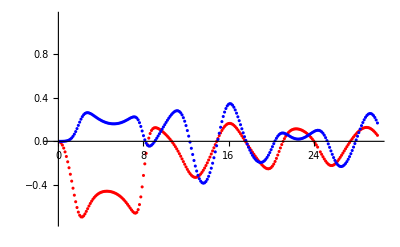

```mathematica
ListPlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v4kTr1[[All,1]],Re[v4kTr1[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

#### b = 0.1

```mathematica
v2kT={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.1,0};
kT=0.25*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$210629 near {ϕ$210629} = {3.77963}. NIntegrate obtained -6.80615×10^-13 and 4.13938×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$269569 near {ϕ$269569} = {6.12082642907296292644758750611799769103527069091796875}. NIntegrate obtained 8.30516×10^-14 and 2.27662×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$348353 near {ϕ$348353} = {6.001928524374696760634861902872216887772083282470703125}. NIntegrate obtained -1.94428×10^-14 and 1.73353×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.25,{0.0021463,-1.28626×10^-14}},{0.5,{0.00868605,6.64234×10^-15}},{0.75,{0.0198684,-3.78716×10^-15}},{1.,{0.0360553,3.33933×10^-14}},{1.25,{0.0577168,3.76078×10^-14}},{1.5,{0.0854292,-4.10588×10^-14}},{1.75,{0.119865,2.91799×10^-12}},{2.,{0.161763,-2.75788×10^-12}},{2.25,{0.211849,3.54951×10^-13}},{2.5,{0.27068,1.12891×10^-12}},{2.75,{0.338333,2.32364×10^-12}},{3.,{0.413874,-2.69565×10^-12}},{3.25,{0.494497,8.83901×10^-12}},{3.5,{0.574373,-9.53273×10^-14}},{3.75,{0.643559,8.35955×10^-17}},{4.,{0.687989,-1.03748×10^-9}},{4.25,{0.692155,1.52666×10^-12}},{4.5,{0.645172,-5.19713×10^-11}},{4.75,{0.547549,-1.03885×10^-10}},{5.,{0.413,-6.77529×10^-12}},{5.25,{0.262688,-8.42856×10^-11}},{5.5,{0.116424,-2.73326×10^-13}},{5.75,{-0.0128447,-1.34284×10^-11}},{6.,{-0.119525,-6.36056×10^-12}},{6.25,{-0.203123,-1.51258×10^-11}},{6.5,{-0.265723,-7.02925×10^-11}},{6.75,{-0.310225,-1.79956×10^-11}},{7.,{-0.33942,-3.55439×10^-11}},{7.25,{-0.355597,-3.9182×10^-11}},{7.5,{-0.360438,-2.09936×10^-12}},{7.75,{-0.355048,8.75221×10^-10}},{8.,{-0.340032,-5.0527×10^-12}},{8.25,{-0.315619,6.5638×10^-10}},{8.5,{-0.28184,3.41057×10^-11}},{8.75,{-0.238846,-1.2783×10^-11}},{9.,{-0.18748,-6.26604×10^-10}},{9.25,{-0.130281,-2.44963×10^-10}},{9.5,{-0.072953,9.70602×10^-11}},{9.75,{-0.0258179,1.63814×10^-10}},{10.,{-0.00347556,2.33753×10^-10}},{10.25,{-0.0200538,-9.56334×10^-11}},{10.5,{-0.0803463,-6.29667×10^-10}},{10.75,{-0.174189,-7.53828×10^-9}},{11.,{-0.281493,1.02428×10^-10}},{11.25,{-0.383404,-7.31797×10^-10}},{11.5,{-0.469051,8.52694×10^-11}},{11.75,{-0.53524,8.13962×10^-11}},{12.,{-0.583182,1.49535×10^-10}},{12.25,{-0.615679,3.86591×10^-10}},{12.5,{-0.635599,-1.0917×10^-8}},{12.75,{-0.645286,-1.50917×10^-9}},{13.,{-0.646432,-8.6774×10^-11}},{13.25,{-0.640115,-3.63653×10^-10}},{13.5,{-0.626895,-1.86649×10^-10}},{13.75,{-0.606902,2.398×10^-10}},{14.,{-0.579912,-5.58597×10^-10}},{14.25,{-0.545446,-1.55497×10^-10}},{14.5,{-0.502905,-1.81869×10^-10}},{14.75,{-0.451833,1.53394×10^-10}},{15.,{-0.392385,1.99254×10^-10}},{15.25,{-0.32611,-9.98784×10^-10}},{15.5,{-0.256984,-2.24173×10^-10}},{15.75,{-0.192287,-3.33128×10^-10}},{16.,{-0.142213,-6.24668×10^-10}},{16.25,{-0.117064,1.2944×10^-9}},{16.5,{-0.122508,-4.00107×10^-10}},{16.75,{-0.156226,-1.61951×10^-9}},{17.,{-0.209105,-2.05875×10^-8}},{17.25,{-0.269872,-4.12376×10^-10}},{17.5,{-0.329292,-3.73732×10^-11}},{17.75,{-0.381727,8.32175×10^-10}},{18.,{-0.42466,-2.04146×10^-9}},{18.25,{-0.457544,-1.4015×10^-9}},{18.5,{-0.480803,-3.02928×10^-8}},{18.75,{-0.495186,2.08409×10^-10}},{19.,{-0.501434,-9.19686×10^-10}},{19.25,{-0.500117,-6.08944×10^-10}},{19.5,{-0.491586,-2.40541×10^-9}},{19.75,{-0.475969,-2.40796×10^-9}},{20.,{-0.453205,-1.98876×10^-9}},{20.25,{-0.4231,-1.72388×10^-8}},{20.5,{-0.385429,-1.80723×10^-9}},{20.75,{-0.340112,-2.67005×10^-9}},{21.,{-0.287477,-2.39857×10^-9}},{21.25,{-0.228654,-2.64255×10^-9}},{21.5,{-0.166058,-6.11159×10^-9}},{21.75,{-0.10382,-1.99483×10^-10}},{22.,{-0.0478536,-1.36342×10^-9}},{22.25,{-0.00511281,1.54892×10^-8}},{22.5,{0.0181226,-6.73691×10^-9}},{22.75,{0.0184297,1.03386×10^-9}},{23.,{-0.00334353,-3.13614×10^-9}},{23.25,{-0.0423993,-1.19756×10^-9}},{23.5,{-0.0918431,1.3867×10^-9}},{23.75,{-0.14481,1.92099×10^-8}},{24.,{-0.195887,-2.0301×10^-9}},{24.25,{-0.241514,-9.83026×10^-10}},{24.5,{-0.279744,3.14355×10^-8}},{24.75,{-0.30975,-1.63262×10^-10}},{25.,{-0.331367,2.54113×10^-8}},{25.25,{-0.344748,2.30925×10^-9}},{25.5,{-0.350146,3.61007×10^-9}},{25.75,{-0.347792,2.86775×10^-9}},{26.,{-0.337842,2.11966×10^-9}},{26.25,{-0.320373,-1.54293×10^-9}},{26.5,{-0.295432,8.85691×10^-9}},{26.75,{-0.263114,4.42113×10^-9}},{27.,{-0.223715,-3.78863×10^-8}},{27.25,{-0.177936,3.90758×10^-9}},{27.5,{-0.127159,3.53197×10^-9}},{27.75,{-0.0737425,2.19927×10^-8}},{28.,{-0.0212211,-5.76377×10^-9}},{28.25,{0.0257622,-1.35453×10^-8}},{28.5,{0.0620071,2.73433×10^-9}},{28.75,{0.0828392,9.53879×10^-9}},{29.,{0.0854259,-3.70989×10^-9}},{29.25,{0.0697351,1.61782×10^-8}},{29.5,{0.0385637,1.04965×10^-8}},{29.75,{-0.00336292,2.01297×10^-8}},{30.,{-0.0507255,8.53026×10^-9}}}

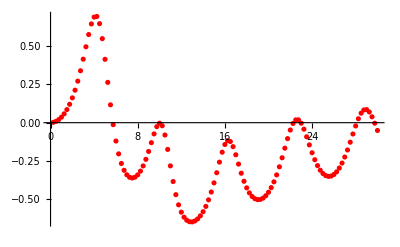

```mathematica
ListPlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
v2kTb02={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.2,0};
kT=0.25*i;
AppendTo[v2kTb02,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9627505 near {ϕ$9627505} = {3.87781}. NIntegrate obtained 1.5668×10^-14 and 2.97948×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9694317 near {ϕ$9694317} = {6.01778009555628290438988869937020353972911834716796875}. NIntegrate obtained 6.97081×10^-14 and 1.03014×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9798316 near {ϕ$9798316} = {0.576679}. NIntegrate obtained -2.65165×10^-13 and 1.0038×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTb02
```

{{0.25,{0.00120005,5.98027×10^-16}},{0.5,{0.00484064,1.14007×10^-14}},{0.75,{0.0110282,-1.07208×10^-13}},{1.,{0.0199274,2.54618×10^-15}},{1.25,{0.0317627,8.41119×10^-14}},{1.5,{0.0468171,1.74042×10^-13}},{1.75,{0.0654236,2.66122×10^-17}},{2.,{0.0879378,-1.04973×10^-12}},{2.25,{0.114674,2.82114×10^-15}},{2.5,{0.14577,9.41872×10^-13}},{2.75,{0.18093,-2.39×10^-12}},{3.,{0.218953,-9.62305×10^-11}},{3.25,{0.256927,2.29637×10^-9}},{3.5,{0.289082,-1.56849×10^-12}},{3.75,{0.305596,-7.2228×10^-18}},{4.,{0.29269,5.62982×10^-9}},{4.25,{0.236452,1.11352×10^-11}},{4.5,{0.131609,-8.38239×10^-13}},{4.75,{-0.0102193,4.43951×10^-12}},{5.,{-0.163272,7.34491×10^-11}},{5.25,{-0.301583,2.63769×10^-10}},{5.5,{-0.410447,4.24856×10^-11}},{5.75,{-0.487181,7.47374×10^-11}},{6.,{-0.535832,-1.49713×10^-11}},{6.25,{-0.562288,4.92507×10^-10}},{6.5,{-0.571781,1.14725×10^-7}},{6.75,{-0.568139,-8.58199×10^-11}},{7.,{-0.553792,3.80709×10^-12}},{7.25,{-0.530035,-2.58482×10^-11}},{7.5,{-0.497289,-6.71574×10^-11}},{7.75,{-0.455334,-4.22624×10^-11}},{8.,{-0.403555,1.01906×10^-11}},{8.25,{-0.341287,-1.26032×10^-10}},{8.5,{-0.268399,-1.12183×10^-9}},{8.75,{-0.186291,-8.49465×10^-11}},{9.,{-0.0993531,-1.2918×10^-9}},{9.25,{-0.0164173,-1.60126×10^-11}},{9.5,{0.0492215,-7.69317×10^-9}},{9.75,{0.0832938,-2.25993×10^-10}},{10.,{0.0773342,-1.64166×10^-10}},{10.25,{0.0340631,-1.29661×10^-9}},{10.5,{-0.0340215,1.26271×10^-8}},{10.75,{-0.111511,-5.3079×10^-10}},{11.,{-0.186194,1.61529×10^-11}},{11.25,{-0.251075,1.45082×10^-11}},{11.5,{-0.303415,1.17462×10^-10}},{11.75,{-0.342991,-6.53192×10^-11}},{12.,{-0.370704,4.75126×10^-12}},{12.25,{-0.387757,-5.45482×10^-11}},{12.5,{-0.395254,-3.81883×10^-10}},{12.75,{-0.394039,1.21226×10^-10}},{13.,{-0.384654,5.00907×10^-11}},{13.25,{-0.367356,-9.45435×10^-11}},{13.5,{-0.342159,-2.70804×10^-10}},{13.75,{-0.308901,-1.37342×10^-10}},{14.,{-0.267352,8.07747×10^-11}},{14.25,{-0.217385,5.09931×10^-8}},{14.5,{-0.159235,4.56522×10^-10}},{14.75,{-0.0939094,-4.57533×10^-10}},{15.,{-0.0236993,5.79058×10^-10}},{15.25,{0.0472688,4.70379×10^-10}},{15.5,{0.112768,4.97195×10^-10}},{15.75,{0.164949,1.41495×10^-9}},{16.,{0.19596,1.21005×10^-9}},{16.25,{0.200449,1.93136×10^-10}},{16.5,{0.177748,1.52422×10^-10}},{16.75,{0.132275,3.02227×10^-10}},{17.,{0.0718378,-3.01646×10^-10}},{17.25,{0.00497991,2.24984×10^-8}},{17.5,{-0.0611226,-5.09428×10^-10}},{17.75,{-0.121542,2.77911×10^-8}},{18.,{-0.173491,-3.43288×10^-8}},{18.25,{-0.21576,-2.02523×10^-10}},{18.5,{-0.248106,4.42768×10^-9}},{18.75,{-0.270776,5.54283×10^-10}},{19.,{-0.284191,-6.1474×10^-10}},{19.25,{-0.288757,2.17543×10^-9}},{19.5,{-0.284779,1.2813×10^-9}},{19.75,{-0.272427,4.64154×10^-10}},{20.,{-0.251758,1.03915×10^-9}},{20.25,{-0.222782,7.31035×10^-10}},{20.5,{-0.18558,-3.26514×10^-8}},{20.75,{-0.140516,2.91041×10^-9}},{21.,{-0.088542,2.57527×10^-9}},{21.25,{-0.0316099,3.63799×10^-9}},{21.5,{0.0268718,4.61162×10^-9}},{21.75,{0.0817394,3.50222×10^-8}},{22.,{0.126278,-8.67206×10^-10}},{22.25,{0.153301,2.68949×10^-8}},{22.5,{0.157117,9.45149×10^-8}},{22.75,{0.135645,-2.49986×10^-9}},{23.,{0.0914338,4.35577×10^-10}},{23.25,{0.0307896,-7.582×10^-10}},{23.5,{-0.0383763,-5.55097×10^-9}},{23.75,{-0.108758,-8.43307×10^-9}},{24.,{-0.174923,2.82652×10^-8}},{24.25,{-0.23355,1.82978×10^-9}},{24.5,{-0.283036,1.54162×10^-8}},{24.75,{-0.322923,-2.24065×10^-9}},{25.,{-0.353388,-1.15135×10^-8}},{25.25,{-0.374873,5.81177×10^-10}},{25.5,{-0.38786,5.09261×10^-8}},{25.75,{-0.392742,-2.52093×10^-9}},{26.,{-0.389767,4.20277×10^-10}},{26.25,{-0.379024,2.53651×10^-9}},{26.5,{-0.360475,7.28979×10^-9}},{26.75,{-0.334035,1.78793×10^-10}},{27.,{-0.299735,1.21742×10^-8}},{27.25,{-0.257999,4.03857×10^-9}},{27.5,{-0.210099,7.70365×10^-9}},{27.75,{-0.158783,1.3498×10^-8}},{28.,{-0.108942,-1.10664×10^-7}},{28.25,{-0.0678878,1.68516×10^-8}},{28.5,{-0.0444845,1.15379×10^-8}},{28.75,{-0.0465873,7.26623×10^-9}},{29.,{-0.0775133,-1.92088×10^-8}},{29.25,{-0.133916,7.15144×10^-9}},{29.5,{-0.206969,1.18129×10^-8}},{29.75,{-0.286134,2.43145×10^-8}},{30.,{-0.362663,2.09513×10^-8}}}

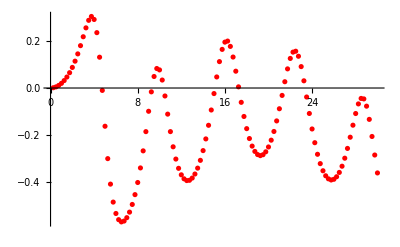

```mathematica
ListPlot[{Transpose[{v2kTb02[[All,1]],Re[v2kTb02[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
v2kTb03={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.3,0};
kT=0.25*i;
AppendTo[v2kTb03,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb03
ListPlot[{Transpose[{v2kTb03[[All,1]],Re[v2kTb03[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$17932229 near {ϕ$17932229} = {6.0340560481230842426736415973209659568965435028076171875}. NIntegrate obtained 1.872×10^-12 and 5.85235×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$18000193 near {ϕ$18000193} = {0.576679}. NIntegrate obtained 2.40176×10^-13 and 1.53719×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$18098288 near {ϕ$18098288} = {0.736213}. NIntegrate obtained 7.61457×10^-15 and 6.79915×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kTb04={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.4,0};
kT=0.25*i;
AppendTo[v2kTb04,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb04
ListPlot[{Transpose[{v2kTb04[[All,1]],Re[v2kTb04[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
v2kTb05={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.5,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb05
ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
Getv2kT[b_]:=Module[{v2kTb05},
v2kTb05={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05

]
```

### r = 2

```mathematica
v2kTr2={};
For[i=1,i≤120,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102101773 near {ϕ$102101773} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102182398 near {ϕ$102182398} = {0.265405}. NIntegrate obtained 3.9576×10^-14 and 4.57269×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102270280 near {ϕ$102270280} = {3.86553}. NIntegrate obtained -1.98307×10^-13 and 6.86125×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kTr2
```

{{0.25,{-0.0119878,4.02166×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{1.,{-0.210431,2.61652×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.75,{-0.605292,1.42908×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.25,{-0.578195,2.59104×10^-9}},{2.5,{-0.526988,1.47112×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{3.,{-0.420273,1.03417×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.5,{-0.277894,-2.47251×10^-11}},{3.75,{-0.176646,-2.85718×10^-10}},{4.,{-0.0478498,-1.51385×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.75,{0.243768,1.80117×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.25,{-0.132316,-8.89064×10^-10}},{5.5,{-0.333077,-8.73848×10^-11}},{5.75,{-0.471218,-5.93729×10^-11}},{6.,{-0.55623,3.19914×10^-14}},{6.25,{-0.603832,-1.34332×10^-10}},{6.5,{-0.623691,8.20746×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{7.,{-0.57304,-8.64402×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.5,{-0.197223,1.84117×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.25,{-0.178263,-2.05153×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.75,{-0.0208926,-9.86587×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.25,{0.199981,-2.5641×10^-8}},{10.5,{0.272559,-2.52265×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.25,{0.116993,-3.66937×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{12.,{-0.174075,-2.16859×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.75,{-0.316903,3.54906×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.25,{-0.315083,-3.31133×10^-7}},{13.5,{-0.286127,-1.17954×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{14.,{-0.208734,-4.3891×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{15.,{-0.04255,3.99352×10^-8}},{15.25,{0.00346786,7.08839×10^-8}},{15.5,{0.045567,-1.39973×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.25,{0.106391,2.01026×10^-7}},{16.5,{0.105642,-8.72217×10^-8}},{16.75,{0.100942,4.88131×10^-6}},{17.,{0.0958046,1.2716×10^-7}},{17.25,{0.0913727,-1.11393×10^-6}},{17.5,{0.0859113,3.63043×10^-7}},{17.75,{0.0745395,-3.76078×10^-7}},{18.,{0.0496753,1.80885×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.75,{-0.146353,1.67139×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.75,{-0.293831,-1.82976×10^-7}},{20.,{-0.258657,-5.80733×10^-9}},{20.25,{-0.197916,-3.56464×10^-8}},{20.5,{-0.117062,-3.83782×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{21.,{0.0491908,3.58877×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.5,{0.0175256,6.44935×10^-7}},{22.75,{0.0272193,1.79738×10^-6}},{23.,{0.0540937,-2.06015×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.5,{0.142333,8.93671×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.25,{0.141413,-3.55586×10^-7}},{24.5,{0.0495847,5.6889×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{25.,{-0.162658,-3.79293×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{26.,{-0.253748,2.287×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.75,{-0.0122859,0.0000242183}},{27.,{0.0595995,-5.06324×10^-6}},{27.25,{0.0839768,3.00352×10^-6}},{27.5,{0.0662111,5.9958×10^-6}},{27.75,{0.0308955,-7.05012×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.25,{0.111579,1.70481×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.75,{0.21089,0.0000138153}},{30.,{0.211163,-2.29551×10^-6}}}

```mathematica
v2kTr2:={{0.25,{-0.011987824066760031,4.021660204770938*^-15}},{0.5,{-0.049673207241812956,3.7457278058170556*^-14}},{0.75,{-0.11478904521078691,-6.03559376280698*^-13}},{1.,{-0.21043098350362172,2.6165229794808745*^-12}},{1.25,{-0.3424213924636071,-5.932366905386802*^-11}},{1.5,{-0.4972644173674114,7.235656197835972*^-12}},{1.75,{-0.6052915303581592,1.429075244880441*^-9}},{2.,{-0.6182392496499612,-5.810031857827077*^-10}},{2.25,{-0.5781947006714055,2.591036488672839*^-9}},{2.5,{-0.5269875405595194,1.4711164766567721*^-9}},{2.75,{-0.47516016706781816,1.0229195109058451*^-10}},{3.,{-0.4202732582450019,1.0341700744266162*^-8}},{3.25,{-0.3567243229875822,-3.0597698867327406*^-9}},{3.5,{-0.2778941132463203,-2.4725129555075954*^-11}},{3.75,{-0.17664645052466302,-2.857184168460874*^-10}},{4.,{-0.04784975487476216,-1.5138502091204945*^-10}},{4.25,{0.10150396010825827,-3.034526798876663*^-10}},{4.5,{0.22858370821263108,-4.3947766735638886*^-8}},{4.75,{0.24376813124225763,1.8011667390216987*^-10}},{5.,{0.0961155046590976,-3.3259205346396855*^-9}},{5.25,{-0.1323163786505354,-8.890644432841953*^-10}},{5.5,{-0.3330770203432369,-8.738483812506843*^-11}},{5.75,{-0.4712182818271504,-5.937291443094876*^-11}},{6.,{-0.5562297130208246,3.19913796332455*^-14}},{6.25,{-0.6038322299731614,-1.343316362613863*^-10}},{6.5,{-0.6236907488011718,8.207461138109764*^-9}},{6.75,{-0.6169306558236888,-9.211967437549099*^-9}},{7.,{-0.5730402045432234,-8.644016844274223*^-9}},{7.25,{-0.46489414819364877,1.0997562851990259*^-9}},{7.5,{-0.2705239563846321,5.503309708162375*^-9}},{7.75,{-0.08788904708786317,-3.762312300738782*^-9}},{8.,{-0.06878499876237988,2.062934171328411*^-9}},{8.25,{-0.13855980875570828,2.4672428806698927*^-8}},{8.5,{-0.1972233342729097,1.8411741660851327*^-8}},{8.75,{-0.22212255068948256,-6.6979270358956116*^-9}},{9.,{-0.21488978872445233,-6.141738387451158*^-8}},{9.25,{-0.17826266524096887,-2.051531306447595*^-9}},{9.5,{-0.11309202110082736,-1.1638647567396398*^-8}},{9.75,{-0.020892587762830508,-9.865868821041999*^-9}},{10.,{0.09054919508087318,-4.2111091151572704*^-9}},{10.25,{0.19998117139037958,-2.5640980954645315*^-8}},{10.5,{0.27255893481872134,-2.5226475475485584*^-8}},{10.75,{0.2784054912830643,1.9457869988174764*^-8}},{11.,{0.21736551866818704,-1.3881977661241984*^-8}},{11.25,{0.11699320833341034,-3.669374258505795*^-8}},{11.5,{0.007946491096557571,-3.0161545891453254*^-8}},{11.75,{-0.09135122158518404,-1.5965272568449384*^-8}},{12.,{-0.1740747105500865,-2.1685916430472374*^-8}},{12.25,{-0.23921346247044006,-8.451316743334802*^-8}},{12.5,{-0.2870718920558613,-1.982937774962435*^-8}},{12.75,{-0.3169030155488351,3.5490647835805426*^-9}},{13.,{-0.32660082331163026,-2.8515596397540252*^-8}},{13.25,{-0.3150826770163598,-3.3113331079062216*^-7}},{13.5,{-0.2861269844674669,-1.1795391829366478*^-8}},{13.75,{-0.24823422412547339,2.3198299137986173*^-8}},{14.,{-0.20873437925488786,-4.389104128178838*^-8}},{14.25,{-0.16984608245571084,-4.89879500666019*^-7}},{14.5,{-0.13017560847174398,6.184682738605995*^-8}},{14.75,{-0.08784106737906038,1.6594349754732864*^-8}},{15.,{-0.04254995956358663,3.993520295392406*^-8}},{15.25,{0.0034678590094145696,7.088385296176046*^-8}},{15.5,{0.04556701897393032,-1.399729579663612*^-7}},{15.75,{0.07839062730020495,5.1250510564552584*^-8}},{16.,{0.0985327605168615,-7.632447693700044*^-8}},{16.25,{0.10639129959902074,2.0102555044861213*^-7}},{16.5,{0.10564208855686347,-8.722169067149654*^-8}},{16.75,{0.10094200603502346,4.881310529160645*^-6}},{17.,{0.09580462082990722,1.2715956523462664*^-7}},{17.25,{0.09137267296802175,-1.1139344097709211*^-6}},{17.5,{0.08591131235606088,3.630425420047259*^-7}},{17.75,{0.07453945791927896,-3.760776347009525*^-7}},{18.,{0.049675311727773105,1.8088544652417546*^-7}},{18.25,{0.0037369064960524213,-3.881291007818384*^-8}},{18.5,{-0.06487441839789523,-7.504634122237701*^-8}},{18.75,{-0.14635259854413163,1.6713926656929236*^-7}},{19.,{-0.2223394936121759,-9.855807890584442*^-7}},{19.25,{-0.2763404644149648,2.9786311794264595*^-7}},{19.5,{-0.3004303974514488,4.526143781771961*^-7}},{19.75,{-0.29383092258985205,-1.8297621045377837*^-7}},{20.,{-0.2586571861680565,-5.807329373674459*^-9}},{20.25,{-0.19791592732417773,-3.56464229241631*^-8}},{20.5,{-0.11706163713724087,-3.8378223592391937*^-7}},{20.75,{-0.027978338831833118,-2.8993007169538167*^-8}},{21.,{0.04919075632523607,3.5887682664500664*^-8}},{21.25,{0.09359462033980777,-1.6138011099817484*^-7}},{21.5,{0.09876418900096838,-3.1807042254158034*^-8}},{21.75,{0.07698132417821239,1.1399450959934535*^-7}},{22.,{0.04752343589987835,-9.03807550491679*^-7}},{22.25,{0.025186275402015297,-3.222073353158401*^-8}},{22.5,{0.017525581012597432,6.449353827038066*^-7}},{22.75,{0.027219256993020746,1.7973768565229199*^-6}},{23.,{0.054093742755611504,-2.0601498207439842*^-7}},{23.25,{0.09504526222913665,4.87946655466399*^-6}},{23.5,{0.14233277263985247,8.936711146175832*^-7}},{23.75,{0.1803055935157353,8.290006065109786*^-7}},{24.,{0.18619713545718108,1.4602462250928072*^-7}},{24.25,{0.14141327141879298,-3.555861578471053*^-7}},{24.5,{0.04958468403958911,5.688899246435387*^-7}},{24.75,{-0.06191660398742835,-9.269826118990355*^-7}},{25.,{-0.16265788629640243,-3.792930986029113*^-6}},{25.25,{-0.2352991707275503,2.3771936421729763*^-6}},{25.5,{-0.2746964410514922,-4.1879214842353814*^-7}},{25.75,{-0.2807425032978987,7.079031465806588*^-7}},{26.,{-0.2537479289747246,2.2870034183045297*^-6}},{26.25,{-0.19420002201416642,-3.1458065954475086*^-6}},{26.5,{-0.10754227412361007,5.7083808032143275*^-6}},{26.75,{-0.012285942907293974,0.000024218257661464282}},{27.,{0.05959945688628011,-5.063241915010969*^-6}},{27.25,{0.08397677527443981,3.003515512151491*^-6}},{27.5,{0.0662110869748594,5.995801804827665*^-6}},{27.75,{0.030895465767032455,-7.050118766113794*^-7}},{28.,{-0.00036248100895704556,1.6479617232993062*^-6}},{28.25,{-0.016264496121349538,-4.679407165003799*^-6}},{28.5,{-0.01253076882196341,-1.3603175297582572*^-6}},{28.75,{0.011625129787136656,1.9290280802050843*^-6}},{29.,{0.05470888192264921,3.634162647815335*^-7}},{29.25,{0.11157878799670498,1.7048071395391025*^-6}},{29.5,{0.1703340706645789,-9.567536440309049*^-6}},{29.75,{0.21088979262887256,0.00001381532986770998}},{30.,{0.21116272031491917,-2.2955058774012284*^-6}}}
```

```mathematica
v2kTr2={};
For[i=1,i≤240,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155450187 near {ϕ$155450187} = {2.57699}. NIntegrate obtained -8.09242×10^-13 and 1.0139×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155526302 near {ϕ$155526302} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155606927 near {ϕ$155606927} = {4.23369}. NIntegrate obtained 1.77029×10^-14 and 2.20759×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.125,{-0.00293846,-3.22797×10^-14}},{0.25,{-0.0119878,4.02166×10^-15}},{0.375,{-0.0274896,8.06758×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.625,{-0.0786963,4.28705×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{0.875,{-0.158429,-6.17377×10^-17}},{1.,{-0.210431,2.61652×10^-12}},{1.125,{-0.271718,-1.06397×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.375,{-0.420021,3.53641×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.625,{-0.562566,-7.13039×10^-9}},{1.75,{-0.605292,1.42908×10^-9}},{1.875,{-0.62223,-3.90179×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.125,{-0.601331,1.24109×10^-9}},{2.25,{-0.578195,2.59104×10^-9}},{2.375,{-0.552817,-3.57247×10^-11}},{2.5,{-0.526988,1.47112×10^-9}},{2.625,{-0.501173,3.04482×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{2.875,{-0.448418,-7.07705×10^-11}},{3.,{-0.420273,1.03417×10^-8}},{3.125,{-0.389976,1.79615×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.375,{-0.319663,-4.44271×10^-11}},{3.5,{-0.277894,-2.47251×10^-11}},{3.625,{-0.230502,2.16695×10^-10}},{3.75,{-0.176646,-2.85718×10^-10}},{3.875,{-0.115746,2.7498×10^-12}},{4.,{-0.0478498,-1.51385×10^-10}},{4.125,{0.0257362,5.98577×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.375,{0.172664,1.71001×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.625,{0.256093,-1.35779×10^-10}},{4.75,{0.243768,1.80117×10^-10}},{4.875,{0.187961,2.44382×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.125,{-0.0161986,9.39926×10^-10}},{5.25,{-0.132316,-8.89064×10^-10}},{5.375,{-0.240029,1.53059×10^-9}},{5.5,{-0.333077,-8.73848×10^-11}},{5.625,{-0.409818,2.59413×10^-8}},{5.75,{-0.471218,-5.93729×10^-11}},{5.875,{-0.519297,-1.65977×10^-7}},{6.,{-0.55623,3.19914×10^-14}},{6.125,{-0.58392,-9.15752×10^-10}},{6.25,{-0.603832,-1.34332×10^-10}},{6.375,{-0.616939,-5.77897×10^-9}},{6.5,{-0.623691,8.20746×10^-9}},{6.625,{-0.623961,-9.89742×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{6.875,{-0.600898,-5.27947×10^-10}},{7.,{-0.57304,-8.64402×10^-9}},{7.125,{-0.529286,-1.75417×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.375,{-0.376998,-3.81623×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.625,{-0.164605,-3.38064×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{7.875,{-0.058007,-3.55694×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.125,{-0.101157,1.31209×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.375,{-0.171809,-1.55624×10^-7}},{8.5,{-0.197223,1.84117×10^-8}},{8.625,{-0.213924,-1.32234×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{8.875,{-0.2223,9.57063×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.125,{-0.200167,7.39934×10^-9}},{9.25,{-0.178263,-2.05153×10^-9}},{9.375,{-0.149237,4.9509×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.625,{-0.070118,-3.76135×10^-9}},{9.75,{-0.0208926,-9.86587×10^-9}},{9.875,{0.0333654,-2.04069×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.125,{0.147491,-1.285×10^-8}},{10.25,{0.199981,-2.5641×10^-8}},{10.375,{0.243209,-8.28052×10^-9}},{10.5,{0.272559,-2.52265×10^-8}},{10.625,{0.284694,-2.42728×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{10.875,{0.254908,-4.16011×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.125,{0.169974,-9.59871×10^-9}},{11.25,{0.116993,-3.66937×10^-8}},{11.375,{0.062076,2.75005×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.625,{-0.0435514,1.25449×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{11.875,{-0.134919,4.47874×10^-9}},{12.,{-0.174075,-2.16859×10^-8}},{12.125,{-0.208816,5.94535×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.375,{-0.26531,3.69644×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.625,{-0.304354,-8.21445×10^-7}},{12.75,{-0.316903,3.54906×10^-9}},{12.875,{-0.324407,-4.23101×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.125,{-0.323405,6.47479×10^-9}},{13.25,{-0.315083,-3.31133×10^-7}},{13.375,{-0.302306,-1.48647×10^-8}},{13.5,{-0.286127,-1.17954×10^-8}},{13.625,{-0.267735,3.28228×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{13.875,{-0.228432,-6.87637×10^-7}},{14.,{-0.208734,-4.3891×10^-8}},{14.125,{-0.189261,-4.57546×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.375,{-0.150243,1.1607×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.625,{-0.109409,-1.70999×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{14.875,{-0.0654788,-2.8936×10^-7}},{15.,{-0.04255,3.99352×10^-8}},{15.125,{-0.0193773,-1.14271×10^-7}},{15.25,{0.00346786,7.08839×10^-8}},{15.375,{0.0253547,1.15384×10^-7}},{15.5,{0.045567,-1.39973×10^-7}},{15.625,{0.0634293,2.49909×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{15.875,{0.0901181,-1.75114×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.125,{0.103822,3.03108×10^-7}},{16.25,{0.106391,2.01026×10^-7}},{16.375,{0.106796,-1.23426×10^-8}},{16.5,{0.105642,-8.72217×10^-8}},{16.625,{0.103523,-1.23856×10^-7}},{16.75,{0.100942,4.88131×10^-6}},{16.875,{0.0982963,-1.11533×10^-7}},{17.,{0.0958046,1.2716×10^-7}},{17.125,{0.0935357,-4.97007×10^-8}},{17.25,{0.0913727,-1.11393×10^-6}},{17.375,{0.0890004,-2.21538×10^-7}},{17.5,{0.0859113,3.63043×10^-7}},{17.625,{0.0813924,6.56037×10^-8}},{17.75,{0.0745395,-3.76078×10^-7}},{17.875,{0.0643234,-9.3084×10^-8}},{18.,{0.0496753,1.80885×10^-7}},{18.125,{0.0296671,-1.62992×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.375,{-0.0280447,-5.57077×10^-7}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.625,{-0.105059,1.05725×10^-7}},{18.75,{-0.146353,1.67139×10^-7}},{18.875,{-0.186234,-2.95609×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.125,{-0.252803,-1.28795×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.375,{-0.292282,-1.51723×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.625,{-0.30086,-5.61182×10^-9}},{19.75,{-0.293831,-1.82976×10^-7}},{19.875,{-0.27965,7.56013×10^-8}},{20.,{-0.258657,-5.80733×10^-9}},{20.125,{-0.231244,4.68169×10^-7}},{20.25,{-0.197916,-3.56464×10^-8}},{20.375,{-0.159464,4.01358×10^-6}},{20.5,{-0.117062,-3.83782×10^-7}},{20.625,{-0.0724435,-1.7726×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{20.875,{0.0135613,-6.27892×10^-7}},{21.,{0.0491908,3.58877×10^-8}},{21.125,{0.0763669,7.78635×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.375,{0.100664,3.68085×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.625,{0.0900206,7.76105×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{21.875,{0.062108,8.71355×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.125,{0.0348625,-2.6805×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.375,{0.0192761,8.66755×10^-7}},{22.5,{0.0175256,6.44935×10^-7}},{22.625,{0.0201537,-2.18465×10^-6}},{22.75,{0.0272193,1.79738×10^-6}},{22.875,{0.0386201,6.45531×10^-7}},{23.,{0.0540937,-2.06015×10^-7}},{23.125,{0.0731796,-3.11281×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.375,{0.118658,4.8467×10^-7}},{23.5,{0.142333,8.93671×10^-7}},{23.625,{0.163801,9.93536×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{23.875,{0.188747,5.98951×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.125,{0.170598,-2.98305×10^-6}},{24.25,{0.141413,-3.55586×10^-7}},{24.375,{0.100039,5.0957×10^-8}},{24.5,{0.0495847,5.6889×10^-7}},{24.625,{-0.00581629,-5.51953×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{24.875,{-0.115076,-3.58317×10^-6}},{25.,{-0.162658,-3.79293×10^-6}},{25.125,{-0.20301,1.00166×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.375,{-0.2592,-2.61543×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.625,{-0.28185,-8.15799×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{25.875,{-0.271374,2.55686×10^-6}},{26.,{-0.253748,2.287×10^-6}},{26.125,{-0.227906,-2.63723×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.375,{-0.153499,1.15036×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.625,{-0.0591728,-2.80712×10^-6}},{26.75,{-0.0122859,0.0000242183}},{26.875,{0.0286373,-2.13003×10^-6}},{27.,{0.0595995,-5.06324×10^-6}},{27.125,{0.0781301,-1.24174×10^-8}},{27.25,{0.0839768,3.00352×10^-6}},{27.375,{0.0789721,8.25448×10^-7}},{27.5,{0.0662111,5.9958×10^-6}},{27.625,{0.0491569,5.96917×10^-7}},{27.75,{0.0308955,-7.05012×10^-7}},{27.875,{0.0138322,-3.94388×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.125,{-0.0106083,-3.35565×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.375,{-0.0169503,-2.87284×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.625,{-0.00296676,-2.84631×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{28.875,{0.0310039,-4.83206×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.125,{0.0819674,1.19561×10^-6}},{29.25,{0.111579,1.70481×10^-6}},{29.375,{0.141809,2.83452×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.625,{0.194361,-0.0000101693}},{29.75,{0.21089,0.0000138153}},{29.875,{0.217129,2.58088×10^-6}},{30.,{0.211163,-2.29551×10^-6}}}

```mathematica
v4kTr2={};
For[i=1,i≤240,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr2,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52117891 near {ϕ$52117891} = {2.57699}. NIntegrate obtained -2.13696×10^-10 and 5.71811×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52160550 near {ϕ$52160550} = {0.638038}. NIntegrate obtained -1.81144×10^-10 and 1.68133×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52222889 near {ϕ$52222889} = {4.23369}. NIntegrate obtained 7.62309×10^-12 and 9.60949×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.125,{-2.85485×10^-6,-8.52408×10^-12}},{0.25,{-0.0000450366,-3.20769×10^-11}},{0.375,{-0.000221186,3.47401×10^-12}},{0.5,{-0.000664018,4.63623×10^-11}},{0.625,{-0.00149749,-3.71232×10^-12}},{0.75,{-0.00275896,-1.02562×10^-10}},{0.875,{-0.00428093,-5.39724×10^-10}},{1.,{-0.00552405,-1.29011×10^-10}},{1.125,{-0.00537823,6.15613×10^-10}},{1.25,{-0.00204371,9.43163×10^-11}},{1.375,{0.00669274,1.98422×10^-7}},{1.5,{0.0223494,2.79419×10^-10}},{1.625,{0.0440204,8.89417×10^-9}},{1.75,{0.0677111,3.07586×10^-9}},{1.875,{0.0882886,-1.03954×10^-8}},{2.,{0.102348,-1.71107×10^-8}},{2.125,{0.109145,-1.31702×10^-8}},{2.25,{0.109629,-1.74448×10^-9}},{2.375,{0.105211,1.49349×10^-11}},{2.5,{0.0971168,1.09717×10^-8}},{2.625,{0.0862055,-1.21584×10^-8}},{2.75,{0.073006,-4.48841×10^-9}},{2.875,{0.0578014,-3.0746×10^-9}},{3.,{0.0407041,-3.25519×10^-9}},{3.125,{0.0217148,-2.06561×10^-8}},{3.25,{0.000765831,2.77696×10^-9}},{3.375,{-0.0222386,1.63192×10^-9}},{3.5,{-0.0473775,9.4894×10^-10}},{3.625,{-0.0746471,-3.48448×10^-9}},{3.75,{-0.103857,-6.8535×10^-9}},{3.875,{-0.134467,-1.80264×10^-7}},{4.,{-0.165318,-3.99831×10^-9}},{4.125,{-0.194299,1.02074×10^-8}},{4.25,{-0.21793,2.07803×10^-9}},{4.375,{-0.23112,7.48883×10^-8}},{4.5,{-0.227661,-1.14302×10^-11}},{4.625,{-0.201862,1.76342×10^-10}},{4.75,{-0.1516,1.02072×10^-7}},{4.875,{-0.0808679,9.90756×10^-8}},{5.,{0.000583918,2.81542×10^-7}},{5.125,{0.0811611,6.47374×10^-7}},{5.25,{0.151896,2.05625×10^-7}},{5.375,{0.208415,8.25339×10^-7}},{5.5,{0.250256,-2.40155×10^-7}},{5.625,{0.279098,-1.04856×10^-6}},{5.75,{0.29735,-1.96877×10^-7}},{5.875,{0.307281,-2.28812×10^-7}},{6.,{0.310726,-7.02969×10^-8}},{6.125,{0.308994,-1.51287×10^-7}},{6.25,{0.302904,2.42607×10^-8}},{6.375,{0.292835,1.19271×10^-10}},{6.5,{0.278762,-1.5048×10^-7}},{6.625,{0.260265,-5.88314×10^-7}},{6.75,{0.236512,-1.68534×10^-8}},{6.875,{0.206252,1.65986×10^-9}},{7.,{0.167916,-2.69827×10^-7}},{7.125,{0.120037,-2.55269×10^-9}},{7.25,{0.0625055,2.75555×10^-9}},{7.375,{-0.000747953,-1.49312×10^-7}},{7.5,{-0.0581051,1.45156×10^-8}},{7.625,{-0.0903664,6.67833×10^-10}},{7.75,{-0.081687,-8.59465×10^-10}},{7.875,{-0.0345259,-5.57171×10^-9}},{8.,{0.0323104,4.22472×10^-9}},{8.125,{0.0998864,-1.11887×10^-10}},{8.25,{0.158304,7.83496×10^-8}},{8.375,{0.205201,1.15375×10^-7}},{8.5,{0.241689,-8.27709×10^-9}},{8.625,{0.269763,-2.57901×10^-8}},{8.75,{0.291242,-3.93728×10^-9}},{8.875,{0.307479,1.61628×10^-8}},{9.,{0.319344,-4.17552×10^-8}},{9.125,{0.327289,1.16495×10^-8}},{9.25,{0.331402,5.48166×10^-9}},{9.375,{0.331449,6.13137×10^-9}},{9.5,{0.326969,1.44425×10^-8}},{9.625,{0.317207,-9.36441×10^-9}},{9.75,{0.301305,-8.02574×10^-9}},{9.875,{0.278384,-2.55199×10^-9}},{10.,{0.247776,1.71242×10^-9}},{10.125,{0.209332,-1.24264×10^-9}},{10.25,{0.163782,-3.32728×10^-8}},{10.375,{0.112995,-1.29745×10^-8}},{10.5,{0.0599784,-5.46859×10^-8}},{10.625,{0.00849308,-5.39589×10^-8}},{10.75,{-0.0376634,2.65554×10^-8}},{10.875,{-0.0754489,-5.00155×10^-8}},{11.,{-0.103112,-2.36578×10^-8}},{11.125,{-0.120307,6.35693×10^-9}},{11.25,{-0.12782,-4.36091×10^-8}},{11.375,{-0.127139,3.9991×10^-8}},{11.5,{-0.119995,4.00072×10^-8}},{11.625,{-0.108177,8.7457×10^-8}},{11.75,{-0.0932949,6.24557×10^-8}},{11.875,{-0.0767878,-1.86222×10^-8}},{12.,{-0.0599607,-3.5111×10^-9}},{12.125,{-0.0440419,-3.11109×10^-9}},{12.25,{-0.0302684,-1.894×10^-8}},{12.375,{-0.0199311,7.3616×10^-9}},{12.5,{-0.0144103,-7.07672×10^-9}},{12.625,{-0.0151231,-1.25445×10^-6}},{12.75,{-0.0233766,2.82846×10^-8}},{12.875,{-0.0400809,-4.05862×10^-8}},{13.,{-0.0653501,9.4619×10^-8}},{13.125,{-0.098075,-1.90543×10^-9}},{13.25,{-0.135671,-5.39956×10^-7}},{13.375,{-0.174255,4.00604×10^-9}},{13.5,{-0.209286,-5.23045×10^-8}},{13.625,{-0.236561,9.44492×10^-8}},{13.75,{-0.253018,-6.71973×10^-9}},{13.875,{-0.257164,-7.20463×10^-7}},{14.,{-0.248971,-1.18658×10^-7}},{14.125,{-0.229428,-9.9523×10^-8}},{14.25,{-0.200066,2.12356×10^-6}},{14.375,{-0.162664,6.22296×10^-8}},{14.5,{-0.118958,5.29122×10^-8}},{14.625,{-0.070635,9.55318×10^-8}},{14.75,{-0.0193636,-3.64719×10^-8}},{14.875,{0.0331884,9.74871×10^-8}},{15.,{0.0851992,8.90809×10^-8}},{15.125,{0.134759,-4.9939×10^-8}},{15.25,{0.179862,9.94328×10^-8}},{15.375,{0.218504,4.00037×10^-8}},{15.5,{0.248854,-5.41841×10^-8}},{15.625,{0.269491,3.24891×10^-7}},{15.75,{0.279568,2.33122×10^-9}},{15.875,{0.278985,-1.4113×10^-7}},{16.,{0.268382,-2.64682×10^-8}},{16.125,{0.249046,-2.12023×10^-8}},{16.25,{0.222737,3.52786×10^-7}},{16.375,{0.191439,-6.02944×10^-8}},{16.5,{0.157137,-1.78496×10^-7}},{16.625,{0.121669,-2.3468×10^-7}},{16.75,{0.0866101,-1.06003×10^-7}},{16.875,{0.0532612,-1.25425×10^-7}},{17.,{0.0226106,7.19376×10^-8}},{17.125,{-0.00457706,-1.895×10^-7}},{17.25,{-0.0277454,9.57698×10^-7}},{17.375,{-0.0465034,3.04128×10^-7}},{17.5,{-0.0606038,-2.07133×10^-7}},{17.625,{-0.0699399,2.89238×10^-7}},{17.75,{-0.0745806,4.22041×10^-7}},{17.875,{-0.0748195,-1.95125×10^-7}},{18.,{-0.0712405,4.2555×10^-7}},{18.125,{-0.0647779,-5.69349×10^-7}},{18.25,{-0.0567419,-4.64131×10^-7}},{18.375,{-0.0487354,-1.14177×10^-6}},{18.5,{-0.0424911,1.60729×10^-7}},{18.625,{-0.0395802,-1.85992×10^-8}},{18.75,{-0.04118,1.80544×10^-7}},{18.875,{-0.0478031,-1.31627×10^-7}},{19.,{-0.0593057,-1.62971×10^-6}},{19.125,{-0.0749776,2.527×10^-7}},{19.25,{-0.093713,2.80693×10^-7}},{19.375,{-0.114257,-1.52291×10^-7}},{19.5,{-0.135316,5.24508×10^-7}},{19.625,{-0.155652,-2.43212×10^-8}},{19.75,{-0.174134,-2.04276×10^-7}},{19.875,{-0.189627,6.81729×10^-8}},{20.,{-0.201043,-9.40917×10^-8}},{20.125,{-0.207248,-1.00115×10^-7}},{20.25,{-0.207075,-1.4198×10^-7}},{20.375,{-0.199379,4.27428×10^-6}},{20.5,{-0.183204,-2.29158×10^-8}},{20.625,{-0.157942,-5.34133×10^-8}},{20.75,{-0.123765,-3.21388×10^-8}},{20.875,{-0.0817937,-6.23656×10^-7}},{21.,{-0.0343156,7.77439×10^-8}},{21.125,{0.0153709,1.23221×10^-7}},{21.25,{0.063498,-8.60337×10^-8}},{21.375,{0.106541,1.47502×10^-6}},{21.5,{0.141857,9.09617×10^-7}},{21.625,{0.168086,2.46256×10^-7}},{21.75,{0.185077,1.47107×10^-7}},{21.875,{0.19358,8.65173×10^-7}},{22.,{0.194878,-1.53981×10^-6}},{22.125,{0.190409,-9.43184×10^-8}},{22.25,{0.181563,1.53773×10^-7}},{22.375,{0.169605,8.46484×10^-7}},{22.5,{0.155371,6.03813×10^-7}},{22.625,{0.139684,-2.86491×10^-6}},{22.75,{0.1231,2.41358×10^-6}},{22.875,{0.106047,9.13363×10^-7}},{23.,{0.0888365,-3.46162×10^-7}},{23.125,{0.0717272,2.45337×10^-7}},{23.25,{0.0549513,3.105×10^-6}},{23.375,{0.0386936,1.04204×10^-6}},{23.5,{0.0231844,1.37131×10^-6}},{23.625,{0.00868817,1.13243×10^-6}},{23.75,{-0.00451258,8.93203×10^-7}},{23.875,{-0.0161409,3.76845×10^-7}},{24.,{-0.0259902,7.16247×10^-7}},{24.125,{-0.0339823,5.67758×10^-6}},{24.25,{-0.0402507,-7.86809×10^-7}},{24.375,{-0.0451373,-2.45242×10^-7}},{24.5,{-0.0491461,1.14205×10^-6}},{24.625,{-0.0528488,-4.01555×10^-7}},{24.75,{-0.0567755,-1.15382×10^-6}},{24.875,{-0.0613441,-3.73939×10^-6}},{25.,{-0.0668336,-4.26591×10^-6}},{25.125,{-0.0733972,1.71526×10^-6}},{25.25,{-0.0810873,2.91196×10^-6}},{25.375,{-0.0898857,-3.00904×10^-6}},{25.5,{-0.0997012,4.10307×10^-7}},{25.625,{-0.110421,-2.81789×10^-6}},{25.75,{-0.121822,-3.949×10^-7}},{25.875,{-0.133599,-3.62332×10^-6}},{26.,{-0.145273,2.15266×10^-6}},{26.125,{-0.156171,-2.04762×10^-6}},{26.25,{-0.165331,3.19256×10^-6}},{26.375,{-0.171499,2.29946×10^-6}},{26.5,{-0.173192,7.05215×10^-6}},{26.625,{-0.168893,-2.65378×10^-7}},{26.75,{-0.157413,7.56049×10^-6}},{26.875,{-0.138361,-2.01444×10^-6}},{27.,{-0.112495,9.50151×10^-7}},{27.125,{-0.0816957,2.19213×10^-7}},{27.25,{-0.0485114,3.53741×10^-6}},{27.375,{-0.0155207,4.50645×10^-7}},{27.5,{0.0152386,6.11524×10^-6}},{27.625,{0.042547,5.57771×10^-7}},{27.75,{0.0658904,-1.00328×10^-6}},{27.875,{0.0853076,-8.92122×10^-7}},{28.,{0.10113,1.15939×10^-6}},{28.125,{0.113811,-3.17975×10^-7}},{28.25,{0.12378,-6.46399×10^-6}},{28.375,{0.131403,-3.97178×10^-6}},{28.5,{0.136954,-2.91748×10^-6}},{28.625,{0.140584,-3.88145×10^-6}},{28.75,{0.142314,2.41274×10^-6}},{28.875,{0.142071,-7.04328×10^-6}},{29.,{0.139676,-5.18286×10^-7}},{29.125,{0.134861,5.45208×10^-6}},{29.25,{0.127341,3.37941×10^-6}},{29.375,{0.116838,4.27324×10^-6}},{29.5,{0.103178,-0.0000115782}},{29.625,{0.0864132,-0.000013119}},{29.75,{0.0669134,7.63103×10^-6}},{29.875,{0.0454435,4.47403×10^-6}},{30.,{0.0231432,0.0211625}}}

{{0.125,{-2.85485×10^-6,-8.52408×10^-12}},{0.25,{-0.0000450366,-3.20769×10^-11}},{0.375,{-0.000221186,3.47401×10^-12}},{0.5,{-0.000664018,4.63623×10^-11}},{0.625,{-0.00149749,-3.71232×10^-12}},{0.75,{-0.00275896,-1.02562×10^-10}},{0.875,{-0.00428093,-5.39724×10^-10}},{1.,{-0.00552405,-1.29011×10^-10}},{1.125,{-0.00537823,6.15613×10^-10}},{1.25,{-0.00204371,9.43163×10^-11}},{1.375,{0.00669274,1.98422×10^-7}},{1.5,{0.0223494,2.79419×10^-10}},{1.625,{0.0440204,8.89417×10^-9}},{1.75,{0.0677111,3.07586×10^-9}},{1.875,{0.0882886,-1.03954×10^-8}},{2.,{0.102348,-1.71107×10^-8}},{2.125,{0.109145,-1.31702×10^-8}},{2.25,{0.109629,-1.74448×10^-9}},{2.375,{0.105211,1.49349×10^-11}},{2.5,{0.0971168,1.09717×10^-8}},{2.625,{0.0862055,-1.21584×10^-8}},{2.75,{0.073006,-4.48841×10^-9}},{2.875,{0.0578014,-3.0746×10^-9}},{3.,{0.0407041,-3.25519×10^-9}},{3.125,{0.0217148,-2.06561×10^-8}},{3.25,{0.000765831,2.77696×10^-9}},{3.375,{-0.0222386,1.63192×10^-9}},{3.5,{-0.0473775,9.4894×10^-10}},{3.625,{-0.0746471,-3.48448×10^-9}},{3.75,{-0.103857,-6.8535×10^-9}},{3.875,{-0.134467,-1.80264×10^-7}},{4.,{-0.165318,-3.99831×10^-9}},{4.125,{-0.194299,1.02074×10^-8}},{4.25,{-0.21793,2.07803×10^-9}},{4.375,{-0.23112,7.48883×10^-8}},{4.5,{-0.227661,-1.14302×10^-11}},{4.625,{-0.201862,1.76342×10^-10}},{4.75,{-0.1516,1.02072×10^-7}},{4.875,{-0.0808679,9.90756×10^-8}},{5.,{0.000583918,2.81542×10^-7}},{5.125,{0.0811611,6.47374×10^-7}},{5.25,{0.151896,2.05625×10^-7}},{5.375,{0.208415,8.25339×10^-7}},{5.5,{0.250256,-2.40155×10^-7}},{5.625,{0.279098,-1.04856×10^-6}},{5.75,{0.29735,-1.96877×10^-7}},{5.875,{0.307281,-2.28812×10^-7}},{6.,{0.310726,-7.02969×10^-8}},{6.125,{0.308994,-1.51287×10^-7}},{6.25,{0.302904,2.42607×10^-8}},{6.375,{0.292835,1.19271×10^-10}},{6.5,{0.278762,-1.5048×10^-7}},{6.625,{0.260265,-5.88314×10^-7}},{6.75,{0.236512,-1.68534×10^-8}},{6.875,{0.206252,1.65986×10^-9}},{7.,{0.167916,-2.69827×10^-7}},{7.125,{0.120037,-2.55269×10^-9}},{7.25,{0.0625055,2.75555×10^-9}},{7.375,{-0.000747953,-1.49312×10^-7}},{7.5,{-0.0581051,1.45156×10^-8}},{7.625,{-0.0903664,6.67833×10^-10}},{7.75,{-0.081687,-8.59465×10^-10}},{7.875,{-0.0345259,-5.57171×10^-9}},{8.,{0.0323104,4.22472×10^-9}},{8.125,{0.0998864,-1.11887×10^-10}},{8.25,{0.158304,7.83496×10^-8}},{8.375,{0.205201,1.15375×10^-7}},{8.5,{0.241689,-8.27709×10^-9}},{8.625,{0.269763,-2.57901×10^-8}},{8.75,{0.291242,-3.93728×10^-9}},{8.875,{0.307479,1.61628×10^-8}},{9.,{0.319344,-4.17552×10^-8}},{9.125,{0.327289,1.16495×10^-8}},{9.25,{0.331402,5.48166×10^-9}},{9.375,{0.331449,6.13137×10^-9}},{9.5,{0.326969,1.44425×10^-8}},{9.625,{0.317207,-9.36441×10^-9}},{9.75,{0.301305,-8.02574×10^-9}},{9.875,{0.278384,-2.55199×10^-9}},{10.,{0.247776,1.71242×10^-9}},{10.125,{0.209332,-1.24264×10^-9}},{10.25,{0.163782,-3.32728×10^-8}},{10.375,{0.112995,-1.29745×10^-8}},{10.5,{0.0599784,-5.46859×10^-8}},{10.625,{0.00849308,-5.39589×10^-8}},{10.75,{-0.0376634,2.65554×10^-8}},{10.875,{-0.0754489,-5.00155×10^-8}},{11.,{-0.103112,-2.36578×10^-8}},{11.125,{-0.120307,6.35693×10^-9}},{11.25,{-0.12782,-4.36091×10^-8}},{11.375,{-0.127139,3.9991×10^-8}},{11.5,{-0.119995,4.00072×10^-8}},{11.625,{-0.108177,8.7457×10^-8}},{11.75,{-0.0932949,6.24557×10^-8}},{11.875,{-0.0767878,-1.86222×10^-8}},{12.,{-0.0599607,-3.5111×10^-9}},{12.125,{-0.0440419,-3.11109×10^-9}},{12.25,{-0.0302684,-1.894×10^-8}},{12.375,{-0.0199311,7.3616×10^-9}},{12.5,{-0.0144103,-7.07672×10^-9}},{12.625,{-0.0151231,-1.25445×10^-6}},{12.75,{-0.0233766,2.82846×10^-8}},{12.875,{-0.0400809,-4.05862×10^-8}},{13.,{-0.0653501,9.4619×10^-8}},{13.125,{-0.098075,-1.90543×10^-9}},{13.25,{-0.135671,-5.39956×10^-7}},{13.375,{-0.174255,4.00604×10^-9}},{13.5,{-0.209286,-5.23045×10^-8}},{13.625,{-0.236561,9.44492×10^-8}},{13.75,{-0.253018,-6.71973×10^-9}},{13.875,{-0.257164,-7.20463×10^-7}},{14.,{-0.248971,-1.18658×10^-7}},{14.125,{-0.229428,-9.9523×10^-8}},{14.25,{-0.200066,2.12356×10^-6}},{14.375,{-0.162664,6.22296×10^-8}},{14.5,{-0.118958,5.29122×10^-8}},{14.625,{-0.070635,9.55318×10^-8}},{14.75,{-0.0193636,-3.64719×10^-8}},{14.875,{0.0331884,9.74871×10^-8}},{15.,{0.0851992,8.90809×10^-8}},{15.125,{0.134759,-4.9939×10^-8}},{15.25,{0.179862,9.94328×10^-8}},{15.375,{0.218504,4.00037×10^-8}},{15.5,{0.248854,-5.41841×10^-8}},{15.625,{0.269491,3.24891×10^-7}},{15.75,{0.279568,2.33122×10^-9}},{15.875,{0.278985,-1.4113×10^-7}},{16.,{0.268382,-2.64682×10^-8}},{16.125,{0.249046,-2.12023×10^-8}},{16.25,{0.222737,3.52786×10^-7}},{16.375,{0.191439,-6.02944×10^-8}},{16.5,{0.157137,-1.78496×10^-7}},{16.625,{0.121669,-2.3468×10^-7}},{16.75,{0.0866101,-1.06003×10^-7}},{16.875,{0.0532612,-1.25425×10^-7}},{17.,{0.0226106,7.19376×10^-8}},{17.125,{-0.00457706,-1.895×10^-7}},{17.25,{-0.0277454,9.57698×10^-7}},{17.375,{-0.0465034,3.04128×10^-7}},{17.5,{-0.0606038,-2.07133×10^-7}},{17.625,{-0.0699399,2.89238×10^-7}},{17.75,{-0.0745806,4.22041×10^-7}},{17.875,{-0.0748195,-1.95125×10^-7}},{18.,{-0.0712405,4.2555×10^-7}},{18.125,{-0.0647779,-5.69349×10^-7}},{18.25,{-0.0567419,-4.64131×10^-7}},{18.375,{-0.0487354,-1.14177×10^-6}},{18.5,{-0.0424911,1.60729×10^-7}},{18.625,{-0.0395802,-1.85992×10^-8}},{18.75,{-0.04118,1.80544×10^-7}},{18.875,{-0.0478031,-1.31627×10^-7}},{19.,{-0.0593057,-1.62971×10^-6}},{19.125,{-0.0749776,2.527×10^-7}},{19.25,{-0.093713,2.80693×10^-7}},{19.375,{-0.114257,-1.52291×10^-7}},{19.5,{-0.135316,5.24508×10^-7}},{19.625,{-0.155652,-2.43212×10^-8}},{19.75,{-0.174134,-2.04276×10^-7}},{19.875,{-0.189627,6.81729×10^-8}},{20.,{-0.201043,-9.40917×10^-8}},{20.125,{-0.207248,-1.00115×10^-7}},{20.25,{-0.207075,-1.4198×10^-7}},{20.375,{-0.199379,4.27428×10^-6}},{20.5,{-0.183204,-2.29158×10^-8}},{20.625,{-0.157942,-5.34133×10^-8}},{20.75,{-0.123765,-3.21388×10^-8}},{20.875,{-0.0817937,-6.23656×10^-7}},{21.,{-0.0343156,7.77439×10^-8}},{21.125,{0.0153709,1.23221×10^-7}},{21.25,{0.063498,-8.60337×10^-8}},{21.375,{0.106541,1.47502×10^-6}},{21.5,{0.141857,9.09617×10^-7}},{21.625,{0.168086,2.46256×10^-7}},{21.75,{0.185077,1.47107×10^-7}},{21.875,{0.19358,8.65173×10^-7}},{22.,{0.194878,-1.53981×10^-6}},{22.125,{0.190409,-9.43184×10^-8}},{22.25,{0.181563,1.53773×10^-7}},{22.375,{0.169605,8.46484×10^-7}},{22.5,{0.155371,6.03813×10^-7}},{22.625,{0.139684,-2.86491×10^-6}},{22.75,{0.1231,2.41358×10^-6}},{22.875,{0.106047,9.13363×10^-7}},{23.,{0.0888365,-3.46162×10^-7}},{23.125,{0.0717272,2.45337×10^-7}},{23.25,{0.0549513,3.105×10^-6}},{23.375,{0.0386936,1.04204×10^-6}},{23.5,{0.0231844,1.37131×10^-6}},{23.625,{0.00868817,1.13243×10^-6}},{23.75,{-0.00451258,8.93203×10^-7}},{23.875,{-0.0161409,3.76845×10^-7}},{24.,{-0.0259902,7.16247×10^-7}},{24.125,{-0.0339823,5.67758×10^-6}},{24.25,{-0.0402507,-7.86809×10^-7}},{24.375,{-0.0451373,-2.45242×10^-7}},{24.5,{-0.0491461,1.14205×10^-6}},{24.625,{-0.0528488,-4.01555×10^-7}},{24.75,{-0.0567755,-1.15382×10^-6}},{24.875,{-0.0613441,-3.73939×10^-6}},{25.,{-0.0668336,-4.26591×10^-6}},{25.125,{-0.0733972,1.71526×10^-6}},{25.25,{-0.0810873,2.91196×10^-6}},{25.375,{-0.0898857,-3.00904×10^-6}},{25.5,{-0.0997012,4.10307×10^-7}},{25.625,{-0.110421,-2.81789×10^-6}},{25.75,{-0.121822,-3.949×10^-7}},{25.875,{-0.133599,-3.62332×10^-6}},{26.,{-0.145273,2.15266×10^-6}},{26.125,{-0.156171,-2.04762×10^-6}},{26.25,{-0.165331,3.19256×10^-6}},{26.375,{-0.171499,2.29946×10^-6}},{26.5,{-0.173192,7.05215×10^-6}},{26.625,{-0.168893,-2.65378×10^-7}},{26.75,{-0.157413,7.56049×10^-6}},{26.875,{-0.138361,-2.01444×10^-6}},{27.,{-0.112495,9.50151×10^-7}},{27.125,{-0.0816957,2.19213×10^-7}},{27.25,{-0.0485114,3.53741×10^-6}},{27.375,{-0.0155207,4.50645×10^-7}},{27.5,{0.0152386,6.11524×10^-6}},{27.625,{0.042547,5.57771×10^-7}},{27.75,{0.0658904,-1.00328×10^-6}},{27.875,{0.0853076,-8.92122×10^-7}},{28.,{0.10113,1.15939×10^-6}},{28.125,{0.113811,-3.17975×10^-7}},{28.25,{0.12378,-6.46399×10^-6}},{28.375,{0.131403,-3.97178×10^-6}},{28.5,{0.136954,-2.91748×10^-6}},{28.625,{0.140584,-3.88145×10^-6}},{28.75,{0.142314,2.41274×10^-6}},{28.875,{0.142071,-7.04328×10^-6}},{29.,{0.139676,-5.18286×10^-7}},{29.125,{0.134861,5.45208×10^-6}},{29.25,{0.127341,3.37941×10^-6}},{29.375,{0.116838,4.27324×10^-6}},{29.5,{0.103178,-0.0000115782}},{29.625,{0.0864132,-0.000013119}},{29.75,{0.0669134,7.63103×10^-6}},{29.875,{0.0454435,4.47403×10^-6}},{30.,{0.0231432,0.0211625}}}

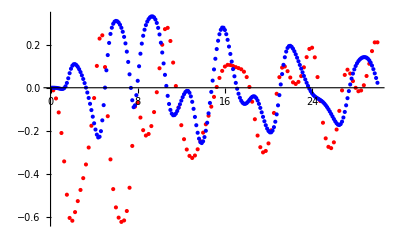

```mathematica
ListPlot[{Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}],Transpose[{v4kTr2[[All,1]],Re[v4kTr2[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

### r = 5

```mathematica
30.0/480
30.0/120
```

0.0625

0.25

```mathematica
v2kTr5={};
For[i=1,i≤480,i++,
x1u=2.5{Cos[π/2],Sin[π/2]};
x3u=2.5{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.0625*i;
AppendTo[v2kTr5,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$649303 near {ϕ$649303} = {0.249129}. NIntegrate obtained -3.93108×10^-12 and 1.05508×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$714657 near {ϕ$714657} = {2.57699}. NIntegrate obtained -2.50466×10^-12 and 3.15885×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$831362 near {ϕ$831362} = {0.108422}. NIntegrate obtained 3.4606×10^-13 and 2.73128×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kTr5
```

{{0.0625,{0.00187827,-9.51362×10^-15}},{0.125,{0.00760703,-2.67618×10^-14}},{0.1875,{0.0174372,9.51111×10^-15}},{0.25,{0.0317627,8.41119×10^-14}},{0.3125,{0.0511219,3.28446×10^-14}},{0.375,{0.0761706,-5.94262×10^-13}},{0.4375,{0.107581,7.85388×10^-11}},{0.5,{0.14577,-9.41796×10^-13}},{0.5625,{0.190244,-1.96997×10^-12}},{0.625,{0.238225,3.6539×10^-17}},{0.6875,{0.282049,-3.07091×10^-13}},{0.75,{0.305596,-1.51285×10^-17}},{0.8125,{0.283129,-1.53381×10^-17}},{0.875,{0.189818,-5.666×10^-11}},{0.9375,{0.0274249,4.04837×10^-11}},{1.,{-0.163272,7.34491×10^-11}},{1.0625,{-0.331837,-3.3843×10^-11}},{1.125,{-0.452666,-7.60882×10^-11}},{1.1875,{-0.52598,2.53209×10^-9}},{1.25,{-0.562288,4.92507×10^-10}},{1.3125,{-0.571986,-1.30245×10^-9}},{1.375,{-0.562199,-1.71808×10^-16}},{1.4375,{-0.536821,-3.14951×10^-9}},{1.5,{-0.497289,-6.71574×10^-11}},{1.5625,{-0.443338,-9.22537×10^-12}},{1.625,{-0.373762,-2.60605×10^-10}},{1.6875,{-0.287579,2.74041×10^-10}},{1.75,{-0.186291,-8.49469×10^-11}},{1.8125,{-0.0777898,1.55167×10^-10}},{1.875,{0.0195023,2.29757×10^-10}},{1.9375,{0.0783655,-4.49359×10^-10}},{2.,{0.0773342,-1.64166×10^-10}},{2.0625,{0.0187566,-8.98622×10^-11}},{2.125,{-0.0724729,-1.21091×10^-9}},{2.1875,{-0.168255,-5.85389×10^-10}},{2.25,{-0.251075,1.45093×10^-11}},{2.3125,{-0.314481,1.75115×10^-10}},{2.375,{-0.358256,-4.80258×10^-9}},{2.4375,{-0.384429,3.03976×10^-10}},{2.5,{-0.395254,3.81883×10^-10}},{2.5625,{-0.392444,3.74951×10^-10}},{2.625,{-0.376989,-2.69525×10^-10}},{2.6875,{-0.349206,-2.51423×10^-10}},{2.75,{-0.308901,-1.37342×10^-10}},{2.8125,{-0.255649,-2.52014×10^-11}},{2.875,{-0.189293,-4.70602×10^-10}},{2.9375,{-0.110816,-7.18403×10^-11}},{3.,{-0.0236993,1.95425×10^-10}},{3.0625,{0.0644434,-2.88426×10^-9}},{3.125,{0.141041,-6.96098×10^-10}},{3.1875,{0.190552,-1.47485×10^-11}},{3.25,{0.200449,1.93135×10^-10}},{3.3125,{0.168248,3.58822×10^-10}},{3.375,{0.10338,-2.39959×10^-10}},{3.4375,{0.0218681,7.49243×10^-10}},{3.5,{-0.0611226,5.09428×10^-10}},{3.5625,{-0.135393,4.46841×10^-9}},{3.625,{-0.195867,-1.41667×10^-8}},{3.6875,{-0.24094,-6.25595×10^-9}},{3.75,{-0.270776,1.10414×10^-9}},{3.8125,{-0.286148,1.15388×10^-8}},{3.875,{-0.287821,-1.75789×10^-10}},{3.9375,{-0.276295,1.17064×10^-8}},{4.,{-0.251758,1.79673×10^-9}},{4.0625,{-0.214244,1.87327×10^-8}},{4.125,{-0.163989,1.6091×10^-8}},{4.1875,{-0.102098,8.53151×10^-9}},{4.25,{-0.0316099,2.35721×10^-8}},{4.3125,{0.041168,-3.7559×10^-9}},{4.375,{0.105758,3.16583×10^-9}},{4.4375,{0.148546,7.49495×10^-9}},{4.5,{0.157117,6.90501×10^-9}},{4.5625,{0.126529,-1.80051×10^-9}},{4.625,{0.0626801,3.52274×10^-9}},{4.6875,{-0.0207116,1.93999×10^-9}},{4.75,{-0.108758,-8.43307×10^-9}},{4.8125,{-0.190374,9.22459×10^-9}},{4.875,{-0.259484,1.23699×10^-8}},{4.9375,{-0.313849,-2.05257×10^-10}},{5.,{-0.353388,-1.15135×10^-8}},{5.0625,{-0.378899,8.53182×10^-8}},{5.125,{-0.391295,-5.54729×10^-10}},{5.1875,{-0.39124,-1.44395×10^-7}},{5.25,{-0.379024,2.53651×10^-9}},{5.3125,{-0.354607,1.32153×10^-8}},{5.375,{-0.317854,-1.79843×10^-9}},{5.4375,{-0.26908,-1.31028×10^-9}},{5.5,{-0.210099,7.70365×10^-9}},{5.5625,{-0.145939,-6.7637×10^-8}},{5.625,{-0.0867771,1.2487×10^-8}},{5.6875,{-0.0482003,1.67998×10^-8}},{5.75,{-0.0465873,7.26623×10^-9}},{5.8125,{-0.0895031,1.75261×10^-9}},{5.875,{-0.169028,1.18715×10^-9}},{5.9375,{-0.2663,2.0838×10^-7}},{6.,{-0.362663,2.09513×10^-8}},{6.0625,{-0.446619,8.34036×10^-9}},{6.125,{-0.513901,1.29313×10^-8}},{6.1875,{-0.564584,1.25451×10^-8}},{6.25,{-0.600474,-3.1679×10^-9}},{6.3125,{-0.623626,1.12682×10^-9}},{6.375,{-0.635682,1.14761×10^-8}},{6.4375,{-0.637654,1.96286×10^-8}},{6.5,{-0.62986,-4.2979×10^-9}},{6.5625,{-0.611978,1.17417×10^-8}},{6.625,{-0.583109,2.27968×10^-8}},{6.6875,{-0.542099,2.28675×10^-8}},{6.75,{-0.488409,5.63667×10^-8}},{6.8125,{-0.424125,-2.74149×10^-8}},{6.875,{-0.357432,4.17674×10^-8}},{6.9375,{-0.305387,8.08985×10^-8}},{7.,{-0.289184,-6.67172×10^-8}},{7.0625,{-0.318627,1.51192×10^-8}},{7.125,{-0.381737,-1.02396×10^-7}},{7.1875,{-0.455392,1.04618×10^-7}},{7.25,{-0.521835,7.64579×10^-8}},{7.3125,{-0.57349,1.71289×10^-7}},{7.375,{-0.609383,4.78886×10^-8}},{7.4375,{-0.631047,-6.64748×10^-8}},{7.5,{-0.6403,-5.1716×10^-8}},{7.5625,{-0.638397,1.19885×10^-8}},{7.625,{-0.625782,-4.21869×10^-8}},{7.6875,{-0.602063,-7.44841×10^-8}},{7.75,{-0.566019,4.55654×10^-8}},{7.8125,{-0.515675,5.34983×10^-7}},{7.875,{-0.448576,4.04653×10^-8}},{7.9375,{-0.362585,6.28332×10^-8}},{8.,{-0.257714,-1.31628×10^-8}},{8.0625,{-0.139455,6.70561×10^-7}},{8.125,{-0.0225617,-1.10532×10^-8}},{8.1875,{0.0692356,3.34221×10^-8}},{8.25,{0.112899,5.68372×10^-8}},{8.3125,{0.101099,-1.34655×10^-7}},{8.375,{0.0468353,-1.06834×10^-7}},{8.4375,{-0.0273667,1.51254×10^-8}},{8.5,{-0.102276,-3.23151×10^-8}},{8.5625,{-0.166694,-3.62559×10^-8}},{8.625,{-0.215977,2.28577×10^-7}},{8.6875,{-0.249084,-2.68709×10^-8}},{8.75,{-0.266413,6.91737×10^-8}},{8.8125,{-0.268607,-1.61674×10^-7}},{8.875,{-0.256085,-1.27576×10^-7}},{8.9375,{-0.228849,6.78733×10^-7}},{9.,{-0.186599,1.23691×10^-7}},{9.0625,{-0.129026,-1.49048×10^-7}},{9.125,{-0.0564103,1.04988×10^-7}},{9.1875,{0.029428,2.87894×10^-7}},{9.25,{0.12381,4.18138×10^-8}},{9.3125,{0.217957,-7.40374×10^-8}},{9.375,{0.299059,-2.65237×10^-9}},{9.4375,{0.352996,-2.26628×10^-7}},{9.5,{0.369614,-2.05534×10^-8}},{9.5625,{0.34762,-1.16208×10^-7}},{9.625,{0.295081,5.10841×10^-7}},{9.6875,{0.225178,8.22645×10^-8}},{9.75,{0.150873,1.01352×10^-9}},{9.8125,{0.08178,9.58714×10^-8}},{9.875,{0.0235373,-2.90812×10^-8}},{9.9375,{-0.021084,-6.21208×10^-8}},{10.,{-0.0511262,2.63447×10^-8}},{10.0625,{-0.0664969,-1.2311×10^-7}},{10.125,{-0.0674301,-3.63156×10^-8}},{10.1875,{-0.0542186,8.38487×10^-8}},{10.25,{-0.0272118,4.93321×10^-8}},{10.3125,{0.0129751,-9.55377×10^-8}},{10.375,{0.0650376,-1.04906×10^-7}},{10.4375,{0.126346,1.1017×10^-7}},{10.5,{0.1922,-1.90066×10^-7}},{10.5625,{0.255323,5.71595×10^-8}},{10.625,{0.306266,6.38575×10^-8}},{10.6875,{0.335312,-4.74362×10^-7}},{10.75,{0.335683,1.09244×10^-7}},{10.8125,{0.306437,6.59557×10^-8}},{10.875,{0.252942,-2.73606×10^-7}},{10.9375,{0.184601,6.48994×10^-7}},{11.,{0.111415,-2.78091×10^-7}},{11.0625,{0.0414898,2.06296×10^-7}},{11.125,{-0.019832,5.38583×10^-7}},{11.1875,{-0.0696419,6.5949×10^-8}},{11.25,{-0.106695,8.61944×10^-8}},{11.3125,{-0.13069,-3.15132×10^-9}},{11.375,{-0.141765,-1.0746×10^-8}},{11.4375,{-0.140225,-2.19807×10^-7}},{11.5,{-0.126436,2.17923×10^-6}},{11.5625,{-0.101022,4.88562×10^-7}},{11.625,{-0.0651661,-2.07598×10^-7}},{11.6875,{-0.0211619,8.06874×10^-8}},{11.75,{0.0268852,8.10428×10^-8}},{11.8125,{0.0725271,-3.76482×10^-7}},{11.875,{0.107208,1.10769×10^-6}},{11.9375,{0.121975,-7.68585×10^-7}},{12.,{0.110585,-1.54395×10^-7}},{12.0625,{0.0724883,5.30302×10^-7}},{12.125,{0.0133273,-7.68792×10^-7}},{12.1875,{-0.0575062,2.68147×10^-7}},{12.25,{-0.130466,6.13348×10^-7}},{12.3125,{-0.198279,2.17777×10^-7}},{12.375,{-0.256589,4.45611×10^-7}},{12.4375,{-0.303384,9.93317×10^-8}},{12.5,{-0.338132,3.90246×10^-7}},{12.5625,{-0.361001,2.27016×10^-7}},{12.625,{-0.372385,-1.57246×10^-7}},{12.6875,{-0.372645,1.23348×10^-7}},{12.75,{-0.362062,7.54228×10^-8}},{12.8125,{-0.340961,-1.36595×10^-9}},{12.875,{-0.310009,5.0653×10^-8}},{12.9375,{-0.270787,1.70774×10^-8}},{13.,{-0.226551,4.07324×10^-7}},{13.0625,{-0.182839,-3.8907×10^-6}},{13.125,{-0.147388,6.44291×10^-7}},{13.1875,{-0.128373,5.01052×10^-8}},{13.25,{-0.131166,-2.26856×10^-7}},{13.3125,{-0.155578,1.43275×10^-7}},{13.375,{-0.195864,5.2168×10^-7}},{13.4375,{-0.243615,5.95385×10^-7}},{13.5,{-0.291043,-2.18392×10^-8}},{13.5625,{-0.332683,-3.26248×10^-7}},{13.625,{-0.365487,-8.03052×10^-7}},{13.6875,{-0.388097,-1.80646×10^-6}},{13.75,{-0.400087,-4.9776×10^-7}},{13.8125,{-0.40135,1.37062×10^-6}},{13.875,{-0.391856,1.12231×10^-7}},{13.9375,{-0.371474,-2.24651×10^-8}},{14.,{-0.340091,9.22968×10^-8}},{14.0625,{-0.297816,-6.17991×10^-7}},{14.125,{-0.245446,-7.11812×10^-7}},{14.1875,{-0.185053,-1.18272×10^-7}},{14.25,{-0.120659,-1.63587×10^-7}},{14.3125,{-0.0585481,-3.97185×10^-7}},{14.375,{-0.00651194,3.40895×10^-7}},{14.4375,{0.028136,-2.93386×10^-7}},{14.5,{0.0412312,-3.99208×10^-7}},{14.5625,{0.0334149,-2.68407×10^-6}},{14.625,{0.00958485,5.60763×10^-7}},{14.6875,{-0.0232547,1.37215×10^-6}},{14.75,{-0.0583227,-4.44815×10^-7}},{14.8125,{-0.0903262,7.7561×10^-7}},{14.875,{-0.115747,6.61899×10^-7}},{14.9375,{-0.132516,9.94378×10^-8}},{15.,{-0.139524,2.5557×10^-7}},{15.0625,{-0.136234,6.58642×10^-6}},{15.125,{-0.122467,1.03718×10^-8}},{15.1875,{-0.0983138,1.0716×10^-6}},{15.25,{-0.0641945,-3.03794×10^-6}},{15.3125,{-0.0210761,3.26524×10^-6}},{15.375,{0.0291489,2.88298×10^-6}},{15.4375,{0.0834496,4.57488×10^-6}},{15.5,{0.137453,8.34081×10^-6}},{15.5625,{0.185688,-0.0000176047}},{15.625,{0.22246,-0.0000157018}},{15.6875,{0.243193,-9.08277×10^-6}},{15.75,{0.245846,-5.62093×10^-7}},{15.8125,{0.231509,8.97303×10^-7}},{15.875,{0.203959,-4.48425×10^-7}},{15.9375,{0.168418,9.78586×10^-7}},{16.,{0.130237,7.32275×10^-7}},{16.0625,{0.0939205,8.92229×10^-7}},{16.125,{0.0628031,-5.51595×10^-7}},{16.1875,{0.0390792,7.53671×10^-7}},{16.25,{0.024033,-1.21263×10^-6}},{16.3125,{0.0183288,-9.49443×10^-7}},{16.375,{0.0221208,-1.5785×10^-6}},{16.4375,{0.0351647,-8.3668×10^-7}},{16.5,{0.0568064,-1.15348×10^-6}},{16.5625,{0.0858201,-4.056×10^-6}},{16.625,{0.120225,4.15545×10^-6}},{16.6875,{0.157189,-1.74074×10^-7}},{16.75,{0.192921,1.79426×10^-6}},{16.8125,{0.223001,-2.01372×10^-6}},{16.875,{0.243034,-2.13638×10^-6}},{16.9375,{0.249614,-3.18475×10^-6}},{17.,{0.241215,-8.1975×10^-7}},{17.0625,{0.218727,-8.91282×10^-7}},{17.125,{0.185153,7.16914×10^-6}},{17.1875,{0.144699,-3.41634×10^-6}},{17.25,{0.101801,0.0000129407}},{17.3125,{0.0604017,-0.0000172939}},{17.375,{0.0233885,7.77322×10^-6}},{17.4375,{-0.00693341,5.86065×10^-6}},{17.5,{-0.0294764,-3.36001×10^-6}},{17.5625,{-0.0436476,-6.12168×10^-6}},{17.625,{-0.0492242,8.44527×10^-6}},{17.6875,{-0.0464992,3.88802×10^-6}},{17.75,{-0.0360584,-5.83945×10^-6}},{17.8125,{-0.0190593,6.57363×10^-6}},{17.875,{0.00275166,0.0000131179}},{17.9375,{0.0266821,-0.0000223242}},{18.,{0.0496026,-3.00711×10^-6}},{18.0625,{0.0673145,-9.66004×10^-6}},{18.125,{0.0760122,4.88671×10^-6}},{18.1875,{0.0726664,-4.17155×10^-6}},{18.25,{0.0561452,5.83503×10^-7}},{18.3125,{0.0274254,4.1702×10^-6}},{18.375,{-0.0106021,-2.42808×10^-6}},{18.4375,{-0.0536567,-0.0000367233}},{18.5,{-0.0977558,0.0000385566}},{18.5625,{-0.139624,0.0000478028}},{18.625,{-0.176337,0.0000470808}},{18.6875,{-0.206181,5.33856×10^-7}},{18.75,{-0.228199,-0.0000347941}},{18.8125,{-0.242394,-1.2297×10^-6}},{18.875,{-0.249032,1.4062×10^-6}},{18.9375,{-0.247865,2.03307×10^-6}},{19.,{-0.239374,-4.07776×10^-7}},{19.0625,{-0.224508,1.67366×10^-6}},{19.125,{-0.20473,2.60358×10^-6}},{19.1875,{-0.182161,5.39534×10^-6}},{19.25,{-0.159736,4.38856×10^-6}},{19.3125,{-0.14085,7.03399×10^-6}},{19.375,{-0.128924,-6.63065×10^-6}},{19.4375,{-0.126447,7.16746×10^-6}},{19.5,{-0.134292,7.81113×10^-6}},{19.5625,{-0.151389,-6.86004×10^-6}},{19.625,{-0.175074,-6.89158×10^-6}},{19.6875,{-0.201939,4.26833×10^-6}},{19.75,{-0.228635,-3.31611×10^-6}},{19.8125,{-0.252385,-3.21962×10^-6}},{19.875,{-0.271173,7.8453×10^-7}},{19.9375,{-0.283665,2.31187×10^-6}},{20.,{-0.28908,-2.55501×10^-6}},{20.0625,{-0.286974,-2.37525×10^-6}},{20.125,{-0.277216,1.73011×10^-6}},{20.1875,{-0.259947,2.69687×10^-6}},{20.25,{-0.235626,8.95174×10^-7}},{20.3125,{-0.205182,1.78944×10^-6}},{20.375,{-0.170173,2.77549×10^-6}},{20.4375,{-0.13288,2.83129×10^-6}},{20.5,{-0.0962752,-4.59551×10^-6}},{20.5625,{-0.0637071,5.52246×10^-6}},{20.625,{-0.0382992,4.47477×10^-6}},{20.6875,{-0.0222558,-2.31405×10^-6}},{20.75,{-0.0162318,5.11918×10^-6}},{20.8125,{-0.0192759,5.43465×10^-6}},{20.875,{-0.0291212,2.62231×10^-6}},{20.9375,{-0.0428993,-1.48457×10^-6}},{21.,{-0.0576515,-3.55781×10^-6}},{21.0625,{-0.0707957,5.43853×10^-7}},{21.125,{-0.0803418,3.28565×10^-6}},{21.1875,{-0.0848674,3.42827×10^-6}},{21.25,{-0.0834555,1.18229×10^-6}},{21.3125,{-0.0756512,3.05165×10^-6}},{21.375,{-0.0613602,-6.9419×10^-6}},{21.4375,{-0.0408975,-4.57995×10^-6}},{21.5,{-0.0149839,-2.1466×10^-6}},{21.5625,{0.0151512,-1.83033×10^-6}},{21.625,{0.047727,1.94122×10^-6}},{21.6875,{0.0804591,2.55744×10^-6}},{21.75,{0.110711,2.76642×10^-6}},{21.8125,{0.135848,-4.1508×10^-6}},{21.875,{0.153657,4.1632×10^-6}},{21.9375,{0.16279,-2.0396×10^-6}},{22.,{0.163046,1.33868×10^-6}},{22.0625,{0.155423,8.37418×10^-7}},{22.125,{0.141819,-2.37544×10^-6}},{22.1875,{0.124636,-3.80089×10^-6}},{22.25,{0.106299,-2.31864×10^-6}},{22.3125,{0.089042,1.29797×10^-7}},{22.375,{0.0746261,1.5337×10^-6}},{22.4375,{0.0643854,-2.60753×10^-6}},{22.5,{0.0591053,2.53356×10^-6}},{22.5625,{0.0592727,-5.951×10^-6}},{22.625,{0.0648922,-3.71061×10^-6}},{22.6875,{0.0755368,-4.84194×10^-6}},{22.75,{0.0905007,4.57987×10^-6}},{22.8125,{0.1086,-8.24016×10^-6}},{22.875,{0.128276,6.18128×10^-6}},{22.9375,{0.147495,7.73778×10^-6}},{23.,{0.164168,5.6917×10^-6}},{23.0625,{0.176272,2.46212×10^-6}},{23.125,{0.182106,-6.70252×10^-6}},{23.1875,{0.180717,-9.5286×10^-8}},{23.25,{0.17204,7.13506×10^-6}},{23.3125,{0.156894,-2.37272×10^-6}},{23.375,{0.136808,-4.31548×10^-7}},{23.4375,{0.11374,-2.2057×10^-7}},{23.5,{0.0897055,-2.62807×10^-6}},{23.5625,{0.0665836,-5.00627×10^-6}},{23.625,{0.0459021,-4.05996×10^-6}},{23.6875,{0.028807,5.41855×10^-6}},{23.75,{0.0160355,4.23592×10^-6}},{23.8125,{0.00796462,1.37217×10^-6}},{23.875,{0.0045998,-8.42889×10^-7}},{23.9375,{0.00559752,0.0000158654}},{24.,{0.0102727,-0.000015479}},{24.0625,{0.0175842,-0.0000158652}},{24.125,{0.0261314,-0.0000118468}},{24.1875,{0.0342889,-0.0000114901}},{24.25,{0.0403083,-0.0000140966}},{24.3125,{0.0424517,-0.0000106687}},{24.375,{0.0394023,8.66157×10^-6}},{24.4375,{0.0304582,3.02412×10^-6}},{24.5,{0.0156676,-5.14007×10^-6}},{24.5625,{-0.00422159,-3.89099×10^-6}},{24.625,{-0.0278071,6.2562×10^-6}},{24.6875,{-0.053406,5.22729×10^-6}},{24.75,{-0.0792635,-5.15668×10^-6}},{24.8125,{-0.103763,-1.2469×10^-6}},{24.875,{-0.12563,-2.67322×10^-6}},{24.9375,{-0.143944,6.89652×10^-6}},{25.,{-0.158058,-6.47648×10^-6}},{25.0625,{-0.167719,7.8366×10^-6}},{25.125,{-0.172923,0.0000105574}},{25.1875,{-0.173786,0.0000128925}},{25.25,{-0.170979,-4.52429×10^-6}},{25.3125,{-0.16531,-6.20154×10^-6}},{25.375,{-0.158138,9.45622×10^-6}},{25.4375,{-0.150536,3.45959×10^-6}},{25.5,{-0.143947,8.411×10^-8}},{25.5625,{-0.131704,2.66337×10^-6}},{25.625,{-0.138786,3.25737×10^-6}},{25.6875,{-0.141701,-7.84736×10^-6}},{25.75,{-0.148407,9.35277×10^-6}},{25.8125,{-0.158219,9.5988×10^-6}},{25.875,{-0.170052,0.0000175757}},{25.9375,{-0.182603,-0.0000176235}},{26.,{-0.194604,0.000017856}},{26.0625,{-0.204854,-0.0000114124}},{26.125,{-0.212318,-8.97856×10^-6}},{26.1875,{-0.216227,9.25861×10^-6}},{26.25,{-0.216216,3.98687×10^-6}},{26.3125,{-0.212066,-4.86104×10^-6}},{26.375,{-0.203777,2.33825×10^-6}},{26.4375,{-0.192705,-6.94479×10^-8}},{26.5,{-0.176187,5.75043×10^-6}},{26.5625,{-0.158239,-0.0000124642}},{26.625,{-0.138904,0.0000117193}},{26.6875,{-0.119372,-0.0000206345}},{26.75,{-0.100939,0.0000207046}},{26.8125,{-0.0847547,0.0000153366}},{26.875,{-0.0716093,0.0000150073}},{26.9375,{-0.0621011,0.0000109212}},{27.,{-0.0560558,-0.0000262341}},{27.0625,{-0.0530413,6.94643×10^-6}},{27.125,{-0.0522451,6.66657×10^-6}},{27.1875,{-0.0526961,-5.39081×10^-6}},{27.25,{-0.0532854,-9.5967×10^-6}},{27.3125,{-0.0530503,9.53654×10^-7}},{27.375,{-0.0511667,5.2778×10^-6}},{27.4375,{-0.0470438,9.02894×10^-7}},{27.5,{-0.0402703,-1.65118×10^-6}},{27.5625,{-0.0307388,-1.31245×10^-6}},{27.625,{-0.01858,-2.30719×10^-6}},{27.6875,{-0.00411215,-4.1598×10^-6}},{27.75,{0.0120858,3.88949×10^-6}},{27.8125,{0.0292209,-0.0000233292}},{27.875,{0.0464346,0.000018096}},{27.9375,{0.0626809,0.000018307}},{28.,{0.0770922,0.0000207222}},{28.0625,{0.0889205,0.0000187141}},{28.125,{0.0976573,0.0000231264}},{28.1875,{0.103151,-0.0000204974}},{28.25,{0.105551,0.0000236377}},{28.3125,{0.105353,0.0000261078}},{28.375,{0.103161,0.0000242608}},{28.4375,{0.0997917,0.0000289655}},{28.5,{0.096039,0.000022203}},{28.5625,{0.0926664,-0.0000239527}},{28.625,{0.0902708,-0.0000206392}},{28.6875,{0.0892836,0.000020259}},{28.75,{0.0899591,0.0000179845}},{28.8125,{0.0923316,3.51639×10^-6}},{28.875,{0.0963348,6.39031×10^-6}},{28.9375,{0.101673,-2.17847×10^-6}},{29.,{0.107872,4.80429×10^-6}},{29.0625,{0.114346,-0.0000102832}},{29.125,{0.120484,0.0000109225}},{29.1875,{0.125579,0.0000215467}},{29.25,{0.129165,-0.0000140173}},{29.3125,{0.130663,7.6624×10^-6}},{29.375,{0.129912,-4.24397×10^-6}},{29.4375,{0.126823,-6.16227×10^-6}},{29.5,{0.121591,-0.000013402}},{29.5625,{0.114471,0.0000140076}},{29.625,{0.106067,0.0000193638}},{29.6875,{0.096842,-0.0000220506}},{29.75,{0.0873166,-9.96285×10^-6}},{29.8125,{0.0779906,-0.0000158677}},{29.875,{0.0693235,0.0000155908}},{29.9375,{0.0615657,0.0000131953}},{30.,{0.054794,-0.0000204072}}}

### Results

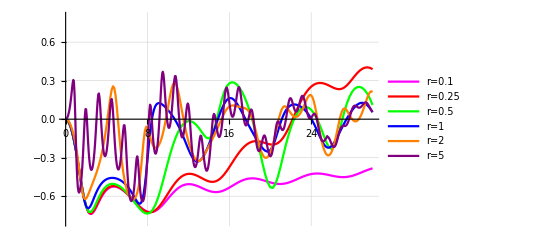

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kTr025[[All,1]],Re[v2kTr025[[All,2,1]]]}],Transpose[{v2kTr05[[All,1]],Re[v2kTr05[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}],Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=0.25","r=0.5","r=1","r=2","r=5"},Joined->{True,True,True,True,True,True}]}]
```

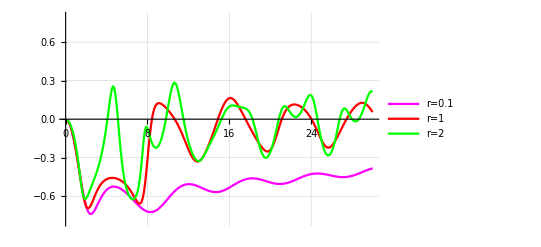

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=1","r=2"},Joined->{True,True,True,True,True,True}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/ppv2

```mathematica
Export["v2kTr01.dat",Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}] ]
Export["v2kTr2.dat",Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}] ]
Export["v2kT.dat",Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]]
```

v2kTr01.dat

v2kTr2.dat

v2kT.dat

```mathematica
Export["v2kTr5.dat",Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}] ]
```

v2kTr5.dat

#### v2 curves

```mathematica
v2[{rA_,θA_},{rB_,θB_},b_,kT_]:=Module[{x1u,x3u,bu},
x1u=rA/2{Cos[θA],Sin[θA]};
x3u=rB/2{Cos[θB],Sin[θB]};
bu={b,0};
NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=π/2;
v2V=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,2π,π/200.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.36837}. NIntegrate obtained -2.84068×10^-14 and 1.71995×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {1.98794}. NIntegrate obtained -1.44361×10^-14 and 1.1567×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {0.785301}. NIntegrate obtained -2.84101×10^-14 and 1.71995×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

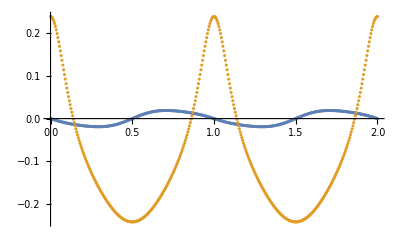

```mathematica
ListPlot[{Transpose[{v2V[[All,1]]/π,v2V[[All,2]][[All,2]]}],Transpose[{v2V[[All,1]]/π,v2V[[All,2]][[All,1]]}]}]
```

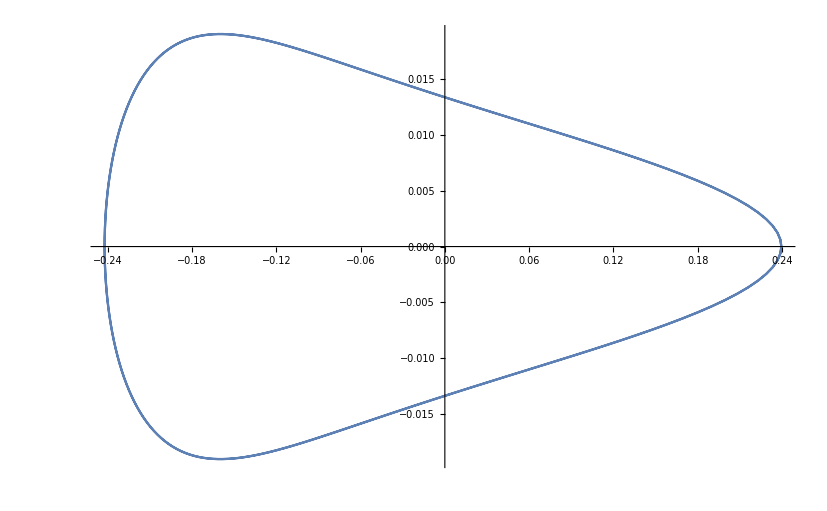

```mathematica
ListPlot[v2V[[All,2]],Joined->True]
```

```mathematica
Export["v2V.dat",v2V]
```

v2V.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=π/4;
v2U=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {5.89039}. NIntegrate obtained 1.03081×10^-8 and 3.18199×10^-12 for the integral and error estimates.

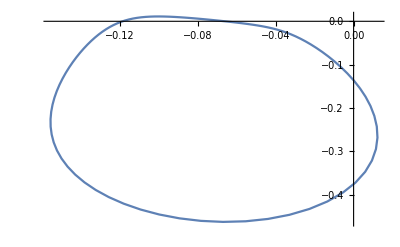

```mathematica
ListPlot[v2U[[All,2]],Joined->True]
```

```mathematica
Export["v2U.dat",v2U]
```

v2U.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=10^-10;
v2H=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.47882}. NIntegrate obtained -4.04942×10^-11 and 4.49613×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.47882}. NIntegrate obtained -4.04887×10^-11 and 4.4961×10^-10 for the integral and error estimates.

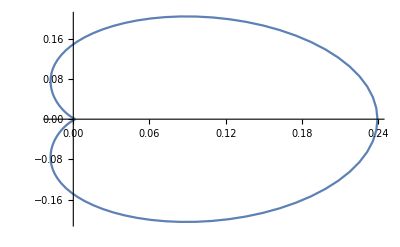

```mathematica
ListPlot[v2H[[All,2]],Joined->True]
```

```mathematica
Export["v2H.dat",v2H]
```

v2H.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=(3π)/4;
v2D=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.53419}. NIntegrate obtained -1.03115×10^-8 and 4.1732×10^-12 for the integral and error estimates.

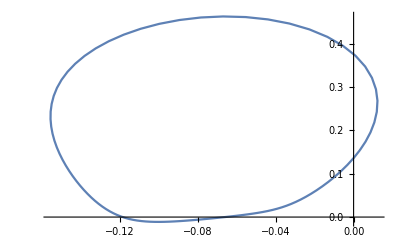

```mathematica
ListPlot[v2D[[All,2]],Joined->True]
```

```mathematica
Export["v2D.dat",v2D]
```

v2D.dat

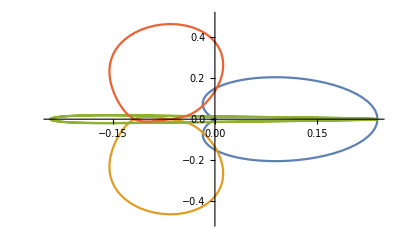

```mathematica
ListPlot[{v2H[[All,2]],v2U[[All,2]],v2V[[All,2]],v2D[[All,2]]},Joined->True,PlotRange->{Full, {-0.5,0.5}}]
```

```mathematica
Clear[dσFig];
dσFig[{bu_,x1u_,x3u_,kT_},{ x1_,x2_,x3_,x4_,qSize_},cs_,rng_:0.35]:=Module[{ϕ,x2u,x4u,p1,p2, sig},
x2u=-x1u;x4u=-x3u;
p1=Show[{Graphics[{RGBColor[0.6,0.6,0.6],Thickness[0.25*qSize],Line[{x3,x4}]}],Graphics[{PointSize[qSize],Red,Point[x3]}],Graphics[{PointSize[qSize],RGBColor[0,0.5,0],Point[x4]}],Graphics[{RGBColor[0.6,0.6,0.6],Thickness[0.25*qSize],Line[{x1,x2}]}],Graphics[{PointSize[qSize],Red,Point[x1]}],Graphics[{PointSize[qSize],RGBColor[0,0.5,0],Point[x2]}]}];
If[Depth[x1u]==2,
sig=NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p2={ParametricPlot[1/sig dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{cs,Thickness[0.015]},AxesLabel->{x,y},LabelStyle->{Black,30}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*),PlotRange->{{-rng,rng},{-rng,rng}},ImageSize->{500,500}]},
sig=Table[NIntegrate[dσHZ[x1u[[i]],x2u[[i]],bu+x3u[[i]],bu+x4u[[i]],{kT,ϕ}],{ϕ,0,2π}],{i,1,Length[x1u]}];
p2=Table[ParametricPlot[(dσHZ[x1u[[i]],-x1u[[i]],bu+x3u[[i]],bu-x3u[[i]],{kT,ϕ}]{Cos[ϕ],Sin[ϕ]})/sig[[i]],{ϕ,0,2π},PlotStyle->cs[[i]],AxesLabel->{x,y},LabelStyle->{Black,30}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*),PlotRange->{{-rng,rng},{-rng,rng}},ImageSize->{500,500}],{i,1,Length[x1u]}]
];
Show[AppendTo[p2,p1]]

]
show[θ1_,θ2_,r0_,b_,kT_, qSize_,showQ_:True]:=Module[{x1u,x3u,bu},
x1u=r0/2{Cos[θ1],Sin[θ1]};
x3u=r0/2{Cos[θ2],Sin[θ2]};
bu={1,0};
showdσHZ[bu,x1u,x3u,kT,showQ,qSize]
]
Clear[figure];
figure[θ1_,θ2_,r0_,b_,kT_, qSize_,cs_,rng_:0.3]:=Module[{x1u,x3u,bu,r,x1,x2,x3,x4,rA,rB,ratio},
If[Depth[r0]==1,
x1u=r0/2{Cos[θ1],Sin[θ1]};
x3u=r0/2{Cos[θ2],Sin[θ2]},
x1u=Table[r0[[i]]/2{Cos[θ1],Sin[θ1]},{i,1,Length[r0]}];
x3u=Table[r0[[i]]/2{Cos[θ2],Sin[θ2]},{i,1,Length[r0]}];
];
bu={b,0};ratio=(rng+0.05)/0.35;
r=0.025*ratio;rB={rng-0.1*ratio,rng};rA={rng,rng};
x1=r*{Cos[θ1],Sin[θ1]};x2=-x1;
x3=r*{Cos[θ2],Sin[θ2]};x4=-x3;
x1=rA+x1;x2=rA+x2;x3=rB+x3;x4=rB+x4;
dσFig[{bu,x1u,x3u,kT},{x1,x2,x3,x4,qSize},cs,rng*(1+0.05/0.3)]
]
v2[{rA_,θA_},{rB_,θB_},b_,kT_]:=Module[{x1u,x3u,bu},
x1u=rA/2{Cos[θA],Sin[θA]};
x3u=rB/2{Cos[θB],Sin[θB]};
bu={b,0};
NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}],{ϕ,0,2π}]
]
```

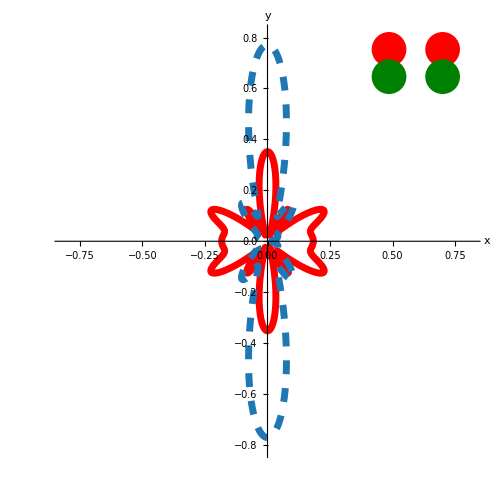

```mathematica
rdp={1,0.1};kT=10;rq=0.05;cs={{Red,Thickness[0.01]},{RGBColor["#1F77B4"],Thickness[0.01],Dashing[{0.02,0.02}]}};kT=10;bT=1;rng=0.7;
r1k10=figure[π/2,π/2,rdp,bT,kT,rq,cs,0.7]
```

```mathematica
rdp={1,0.1};rq=0.05;cs={{Red,Thickness[0.01]},{RGBColor["#1F77B4"],Thickness[0.01],Dashing[{0.02,0.02}]}};kT=30;bT=1;rng=0.7;
r1k30={{figure[0,π/2,rdp,bT,kT,rq,cs,0.3],figure[π/4,π/2,rdp,bT,kT,rq,cs,0.5],figure[π/2,π/2,rdp,bT,kT,rq,cs,0.7],figure[(3π)/4,π/2,rdp,bT,kT,rq,cs,0.5]},
	{figure[0,π/4,rdp,bT,kT,rq,cs,0.4],figure[π/4,π/4,rdp,bT,kT,rq,cs,0.5],figure[π/2,π/4,rdp,bT,kT,rq,cs,0.5],figure[(3π)/4,π/4,rdp,bT,kT,rq,cs,0.5]},
	{figure[10^-10,0,rdp,bT,kT,rq,cs,0.3],figure[π/4,0,rdp,bT,kT,rq,cs,0.4],figure[π/2,0,rdp,bT,kT,rq,cs,0.3],figure[(3π)/4,0,rdp,bT,kT,rq,cs,0.4]},
	{figure[0,3π/4,rdp,bT,kT,rq,cs,0.4],figure[π/4,3 π/4,rdp,bT,kT,rq,cs,0.5],figure[π/2,3 π/4,rdp,bT,kT,rq,cs,0.5],figure[(3π)/4,3 π/4,rdp,bT,kT,rq,cs,0.5]}
};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139017280 near {ϕ$139017280} = {4.33186}. NIntegrate obtained 1.13198×10^-6 and 1.21381×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139017280 near {ϕ$139017280} = {1.9634}. NIntegrate obtained 1.00646×10^-8 and 1.38258×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139137966 near {ϕ$139137966} = {2.40518}. NIntegrate obtained 6.70765×10^-7 and 8.74184×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000128228,-8.82391} lies outside the range of data in the interpolating function. Extrapolation will be used.

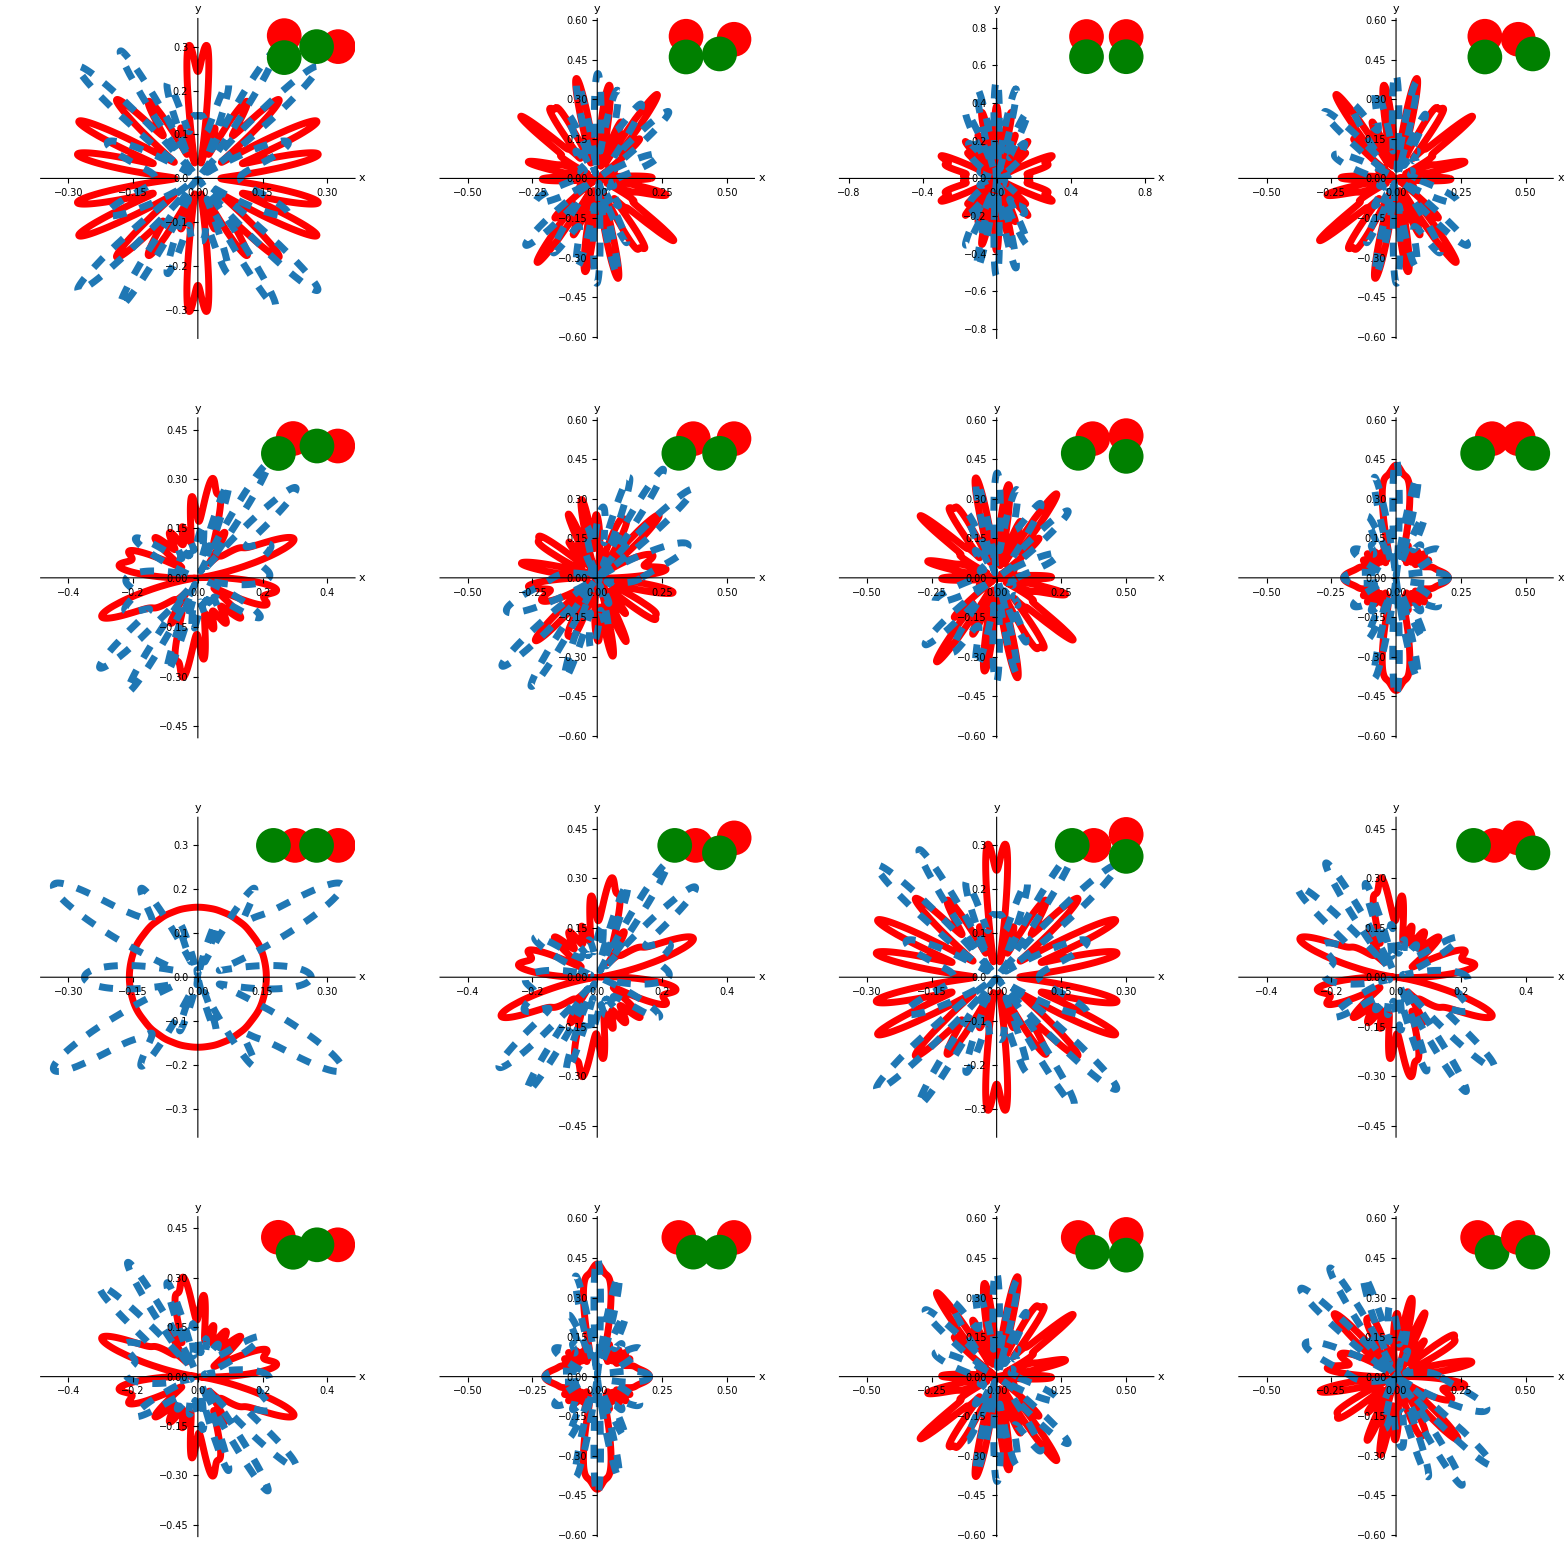

```mathematica
GraphicsGrid[r1k30]
```